# Medical Isotopes

ISOLPHARM SPES INFN from the MEDICIS-PROMED conference presentation by Michelle Ballan 2019.

## Setup

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Terbium 155 Investigation

Notes
• Currently only exists via ISOL spallation experiments. 
• The Dysprosium 156 target would be difficult to make as it isn’t particularly abundant (~0.06%).
• Separation of 156 Dy from bulk Dy by chromatographic methods of separation from Bulk Dy? SILEX? No adequate centrifuge route.
• 155 Tb is used in Uli Koster’s Terbium Theranostic quadruplet. Decays by EC @ t_(1/2) = 5.32 days. 
 • Dysprosium has 7 stable isotopes 156Dy 158Dy 160Dy 161Dy 162Dy 163Dy 164Dy
• The photonuclear production route is:
	• 156 Dy → 155 Dy (γ,n) → 155 Tb (β^+, t_(1/2) = 9.92 h). 
• The 156 Dy Bremsstrahlung average cross section data also hinders this route. Bremsstrahlung data on cross sections from an Elektra medical linac results only in average values for the 155 Dy photonuclear cross section of interest. 
• Other investigated routes could be:
	• 158 Dy (γ,3n) → 155 Tb but no data for this.
	• 156 Dy (γ,p) → 155 Tb but no data for this. May be a beneficial production route if it overlaps!
	• 157 Ho (γ,α) reaction not possible as not stable.
• Other ‘disruptor’ routes could be:
	• 164 Dy (γ, n) no data
	• 156, 158, 161, 162, 163, 164 Dy (γ, 2+n) with no data but which is likely to be higher energy.
	• 158, 160, 161, 162, 163, 164 (γ, p) with no data
	• 156, 158, 160, 161, 162, 163, 164 (γ,α) with no data

## Dysprosium 162→161 (γ, n) [Renstrom et al]

```mathematica
SetDirectory[NotebookDirectory[]];
Dy162data =Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Terbium155/162Dyto161Dy.txt","Table"],2];
```

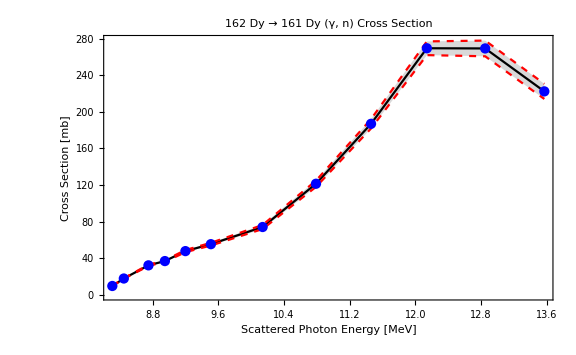

```mathematica
Dy162plot=ListPlot[{Partition[Riffle[Dy162data⟦All,1⟧,Dy162data⟦All,2⟧],2],Partition[Riffle[Dy162data⟦All,1⟧,Dy162data⟦All,2⟧],2],Partition[Riffle[Dy162data⟦All,1⟧,(Dy162data⟦All,2⟧+Dy162data⟦All,3⟧)],2],Partition[Riffle[Dy162data⟦All,1⟧,(Dy162data⟦All,2⟧-Dy162data⟦All,3⟧)],2]},PlotLabel->"162 Dy → 161 Dy (γ, n) Cross Section",PlotStyle->{Blue,Black,{Dashed,Red},{Dashed,Red}},Joined->{False,True,True,True},Frame->True,FrameLabel->{"Scattered Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},Filling->{3->{{4},{LightGray}}},ImageSize->Large]
```

The 162 Tb → 161 Tb Cross Section as a function of scattered photon energy has been measured at the NewSUBARU ICS. 
T. Renstrøm et al, Verification of detailed balance for γ absorption and emission in Dy isotopes, PHYSICAL REVIEW C 98, 054310 (2018)

## Dysprosium 163→162 (γ, n) [Renstrom et al]

```mathematica
SetDirectory[NotebookDirectory[]];
Dy163data =Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Terbium155/163Dyto162Dy.txt","Table"],2];
```

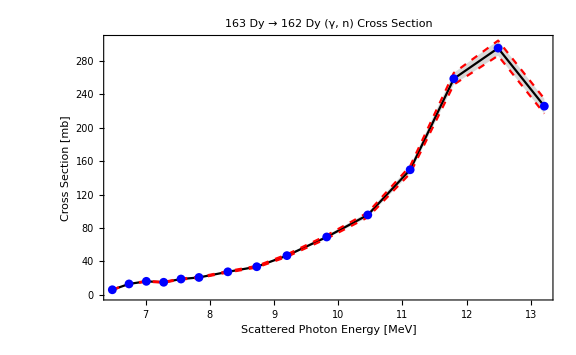

```mathematica
Dy163plot=ListPlot[{Partition[Riffle[Dy163data⟦All,1⟧,Dy163data⟦All,2⟧],2],Partition[Riffle[Dy163data⟦All,1⟧,Dy163data⟦All,2⟧],2],Partition[Riffle[Dy163data⟦All,1⟧,(Dy163data⟦All,2⟧+Dy163data⟦All,3⟧)],2],Partition[Riffle[Dy163data⟦All,1⟧,(Dy163data⟦All,2⟧-Dy163data⟦All,3⟧)],2]},PlotLabel->"163 Dy → 162 Dy (γ, n) Cross Section",PlotStyle->{Blue,Black,{Dashed,Red},{Dashed,Red}},Joined->{False,True,True,True},Frame->True,FrameLabel->{"Scattered Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},Filling->{3->{{4},{LightGray}}},ImageSize->Large]
```

The 163 Dy → 162 Dy Cross Section as a function of scattered photon energy has been measured at the NewSUBARU ICS. 
T. Renstrøm et al, Verification of detailed balance for γ absorption and emission in Dy isotopes, PHYSICAL REVIEW C 98, 054310 (2018)

## Dysprosium Landscape

```mathematica
Dy156CS={{9.44,144},{14,144}};
Dy158CS={{9.04,168},{14,168}};
```

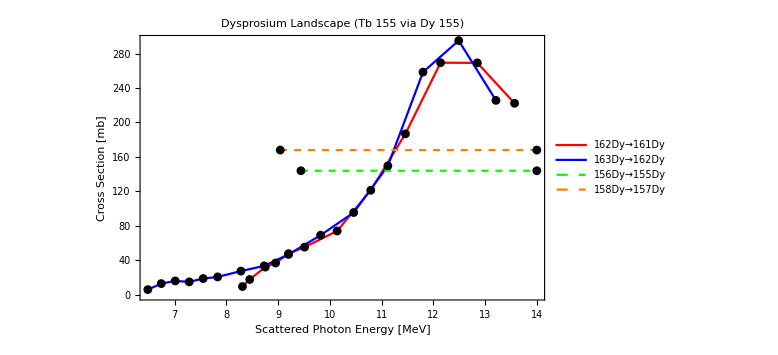

```mathematica
Dyplot=ListPlot[{Partition[Riffle[Dy162data⟦All,1⟧,Dy162data⟦All,2⟧],2],Partition[Riffle[Dy162data⟦All,1⟧,Dy162data⟦All,2⟧],2],Partition[Riffle[Dy163data⟦All,1⟧,Dy163data⟦All,2⟧],2],Partition[Riffle[Dy163data⟦All,1⟧,Dy163data⟦All,2⟧],2],Dy156CS,Dy156CS,Dy158CS,Dy158CS},PlotLabel->"Dysprosium Landscape (Tb 155 via Dy 155)",PlotStyle->{Black,Red,Black,Blue,Black,{Dashed,Green},Black,{Dashed,Orange}},Joined->{False,True,False,True,False,True,False,True},Frame->True,FrameLabel->{"Scattered Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{None,"162Dy→161Dy",None,"163Dy→162Dy",None,"156Dy→155Dy",None,"158Dy→157Dy"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.8}],ImageSize->Large]
```

## Specific Activity Example Calc (Old DIANA)

```mathematica
M=156;(*g/mol*)
NA=6.02*10^23;(*Avogadro's /mol*)
thalf155Dy=10.2; (*hours*)
ΦDIANA=2.93*10^9;(*~photon flux DIANA @ 8 and 18 MeV *)
σ156Dy=144*10^-3*10^-28;
σ156Dypos=188*10^-3*10^-28;
σ156Dyneg=100*10^-3*10^-28;(*156 Dy cross section*)
```

```mathematica
ApM[σ_,Φ_,tirr_,thalf_]:=10^3*NA/M*σ*Φ*(1-Exp[(-Log[2]*tirr)/thalf]);
```

```mathematica
(*Specific Activity in Bq/mg*)
```

```mathematica
SpecAc=Table[{tirr,ApM[σ156Dy,ΦDIANA,tirr,thalf155Dy]/10^3,ApM[σ156Dypos,ΦDIANA,tirr,thalf155Dy]/10^3,ApM[σ156Dyneg,ΦDIANA,tirr,thalf155Dy]/10^3},{tirr,0,100,0.1}];
```

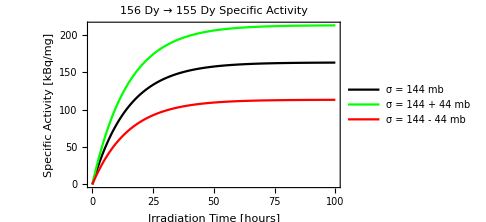

```mathematica
ListLinePlot[{Partition[Riffle[SpecAc⟦All,1⟧,SpecAc⟦All,2⟧],2],Partition[Riffle[SpecAc⟦All,1⟧,SpecAc⟦All,3⟧],2],Partition[Riffle[SpecAc⟦All,1⟧,SpecAc⟦All,4⟧],2]},Frame->True,FrameLabel->{"Irradiation Time [hours]","Specific Activity [kBq/mg]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotStyle->{Black,Green,Red},PlotLabel->"156 Dy → 155 Dy Specific Activity",PlotLegends->Placed[LineLegend[{"σ = 144 mb","σ = 144 + 44 mb","σ = 144 - 44 mb"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.2}],ImageSize->Medium]
```

## Gold 196 Investigation

Notes
• The 197 Au target is easy to produce - Geiger, Marsden + Rutherford used one in gold foil experiment @ Manchester. Nice story!
• 197 Au is the only abundant isotope. History of gold foil targets, easy.
• Potential Theranostic partner of 198 Au as an imaging isotope I think. Gold nano-particles are involved in a lot of cancer research + imaging (by CT) research too, in vogue at the minute. Could radioisotope 196 Au supplement this?
• Lack of medical data on it’s theranostic pairing with 198 Au?
• Gold 196 decays by β^+ (93%) and β^- (7%) with t_(1/2) = 6.61 days.
• Excited Gold “m” states may be useful for medical applications too but no data on them.
• The main photonuclear route is:
	• 197 Au → 196 Au (γ,n) 
• Other investigated routes could be:
	• 198 Hg (γ,p+n) but 198 Hg is ~10% abundant and this seems far more complicated
	• The 197 Hg (γ,p) is not possible as it is not stable.
	• The 200 Tl (γ,α) route is not possible as it is not stable.
• Other Disruptor routes could be:
	• 197 Au (γ,p) with no data (or γ,integer p)
	• 197 Au (γ,α) with no data

## 197 Au → 196 Au (γ,n)

```mathematica
SetDirectory[NotebookDirectory[]];
Plaisir197Au196Au =Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Plaisir_Gold196.txt","Table"],2];
Itoh197Au196Au=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Itoh_Gold196.txt","Table"],2];
Kitatani197Au196Au=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Kitatani_Gold196.txt","Table"],2];

Naik197Au195Au=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Naik_Gold195.txt","Table"],2];
Berman197Au195Au=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Berman_Gold195.txt","Table"],2];

Naik197Au194Au=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Naik_Gold194.txt","Table"],2];
Veyissiere197Au194Au=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Veyissiere_Gold194.txt","Table"],2];

Naik197Au193Au=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Naik_Gold193.txt","Table"],2];
Naik197Au192Au=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Naik_Gold192.txt","Table"],2];
Naik197Au191Au=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Gold196/Naik_Gold191.txt","Table"],2];
```

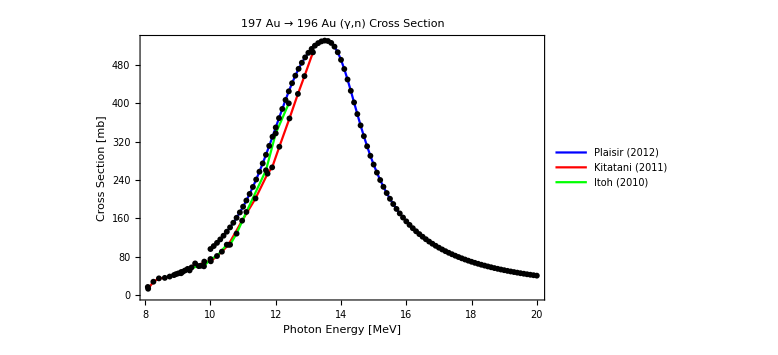

```mathematica
ListPlot[{Partition[Riffle[Plaisir197Au196Au⟦All,1⟧,Plaisir197Au196Au⟦All,2⟧],2],Partition[Riffle[Plaisir197Au196Au⟦All,1⟧,Plaisir197Au196Au⟦All,2⟧],2],Partition[Riffle[Itoh197Au196Au⟦All,1⟧,Itoh197Au196Au⟦All,2⟧],2],Partition[Riffle[Itoh197Au196Au⟦All,1⟧,Itoh197Au196Au⟦All,2⟧],2],Partition[Riffle[Kitatani197Au196Au⟦All,1⟧,Kitatani197Au196Au⟦All,3⟧],2],Partition[Riffle[Kitatani197Au196Au⟦All,1⟧,Kitatani197Au196Au⟦All,3⟧],2]},Joined->{False,True,False,True,False,True},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{18,FontFamily->"Calibri",FontColor->Black},PlotLabel->"197 Au → 196 Au (γ,n) Cross Section",PlotStyle->{Black,Blue,Black,Red,Black,Green},PlotLegends->Placed[LineLegend[{None,"Plaisir (2012)",None,"Kitatani (2011)",None,"Itoh (2010)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.45,0.2}],ImageSize->Large]
```

## 197 Au → 195 Au (γ,2n)

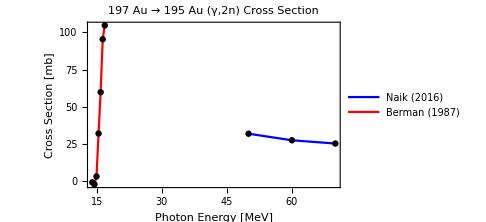

```mathematica
ListPlot[{Partition[Riffle[Naik197Au195Au⟦All,1⟧,Naik197Au195Au⟦All,2⟧],2],Partition[Riffle[Naik197Au195Au⟦All,1⟧,Naik197Au195Au⟦All,2⟧],2],Partition[Riffle[Berman197Au195Au⟦All,1⟧,Berman197Au195Au⟦All,2⟧],2],Partition[Riffle[Berman197Au195Au⟦All,1⟧,Berman197Au195Au⟦All,2⟧],2]},Joined->{False,True},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"197 Au → 195 Au (γ,2n) Cross Section",PlotStyle->{Black,Blue,Black,Red},PlotLegends->Placed[LineLegend[{None,"Naik (2016)",None,"Berman (1987)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.8}],ImageSize->Medium]
```

## 197 Au → 194 Au (γ,3n)

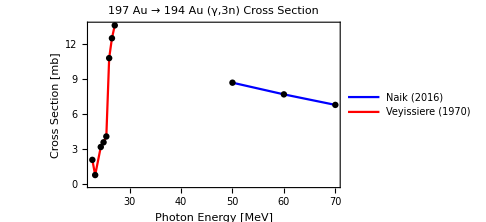

```mathematica
ListPlot[{Partition[Riffle[Naik197Au194Au⟦All,1⟧,Naik197Au194Au⟦All,2⟧],2],Partition[Riffle[Naik197Au194Au⟦All,1⟧,Naik197Au194Au⟦All,2⟧],2],Partition[Riffle[Veyissiere197Au194Au⟦All,1⟧,Veyissiere197Au194Au⟦All,2⟧],2],Partition[Riffle[Veyissiere197Au194Au⟦All,1⟧,Veyissiere197Au194Au⟦All,2⟧],2]},Joined->{False,True},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"197 Au → 194 Au (γ,3n) Cross Section",PlotStyle->{Black,Blue,Black,Red},PlotLegends->Placed[LineLegend[{None,"Naik (2016)",None,"Veyissiere (1970)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.8}],ImageSize->Medium]
```

## 197 Au → 193, 192, 191 Au (γ,(3+)n)

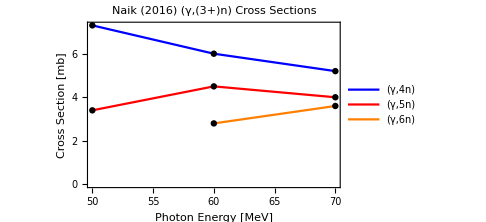

```mathematica
ListPlot[{Partition[Riffle[Naik197Au193Au⟦All,1⟧,Naik197Au193Au⟦All,2⟧],2],Partition[Riffle[Naik197Au193Au⟦All,1⟧,Naik197Au193Au⟦All,2⟧],2],Partition[Riffle[Naik197Au192Au⟦All,1⟧,Naik197Au192Au⟦All,2⟧],2],Partition[Riffle[Naik197Au192Au⟦All,1⟧,Naik197Au192Au⟦All,2⟧],2],Partition[Riffle[Naik197Au191Au⟦All,1⟧,Naik197Au191Au⟦All,2⟧],2],Partition[Riffle[Naik197Au191Au⟦All,1⟧,Naik197Au191Au⟦All,2⟧],2]},Joined->{False,True},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Naik (2016) (γ,(3+)n) Cross Sections",PlotStyle->{Black,Blue,Black,Red,Black,Orange},PlotLegends->Placed[LineLegend[{None,"(γ,4n)",None,"(γ,5n)",None,"(γ,6n)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.2}],ImageSize->Medium]
```

## Gold Photonuclear Landscape

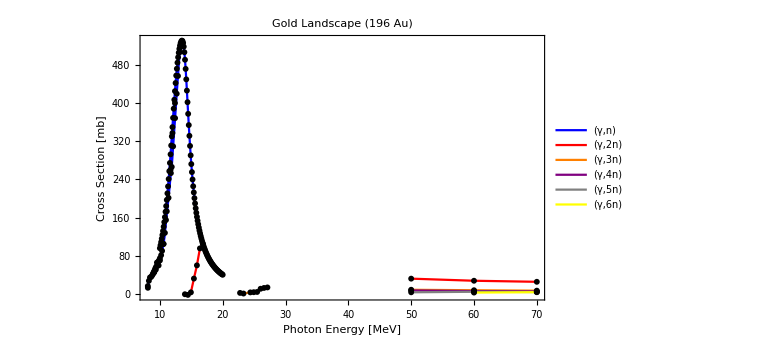

```mathematica
ListPlot[{Partition[Riffle[Plaisir197Au196Au⟦All,1⟧,Plaisir197Au196Au⟦All,2⟧],2],Partition[Riffle[Plaisir197Au196Au⟦All,1⟧,Plaisir197Au196Au⟦All,2⟧],2],Partition[Riffle[Itoh197Au196Au⟦All,1⟧,Itoh197Au196Au⟦All,2⟧],2],Partition[Riffle[Itoh197Au196Au⟦All,1⟧,Itoh197Au196Au⟦All,2⟧],2],Partition[Riffle[Kitatani197Au196Au⟦All,1⟧,Kitatani197Au196Au⟦All,3⟧],2],Partition[Riffle[Kitatani197Au196Au⟦All,1⟧,Kitatani197Au196Au⟦All,3⟧],2],Partition[Riffle[Naik197Au195Au⟦All,1⟧,Naik197Au195Au⟦All,2⟧],2],Partition[Riffle[Naik197Au195Au⟦All,1⟧,Naik197Au195Au⟦All,2⟧],2],Partition[Riffle[Berman197Au195Au⟦All,1⟧,Berman197Au195Au⟦All,2⟧],2],Partition[Riffle[Berman197Au195Au⟦All,1⟧,Berman197Au195Au⟦All,2⟧],2],Partition[Riffle[Naik197Au194Au⟦All,1⟧,Naik197Au194Au⟦All,2⟧],2],Partition[Riffle[Naik197Au194Au⟦All,1⟧,Naik197Au194Au⟦All,2⟧],2],Partition[Riffle[Veyissiere197Au194Au⟦All,1⟧,Veyissiere197Au194Au⟦All,2⟧],2],Partition[Riffle[Veyissiere197Au194Au⟦All,1⟧,Veyissiere197Au194Au⟦All,2⟧],2],Partition[Riffle[Naik197Au193Au⟦All,1⟧,Naik197Au193Au⟦All,2⟧],2],Partition[Riffle[Naik197Au193Au⟦All,1⟧,Naik197Au193Au⟦All,2⟧],2],Partition[Riffle[Naik197Au192Au⟦All,1⟧,Naik197Au192Au⟦All,2⟧],2],Partition[Riffle[Naik197Au192Au⟦All,1⟧,Naik197Au192Au⟦All,2⟧],2],Partition[Riffle[Naik197Au191Au⟦All,1⟧,Naik197Au191Au⟦All,2⟧],2],Partition[Riffle[Naik197Au191Au⟦All,1⟧,Naik197Au191Au⟦All,2⟧],2]},PlotStyle->{Black,Blue,Black,Blue,Black,Blue,Black,Red,Black,Red,Black,Orange,Black,Orange,Black,Purple,Black,Gray,Black,Yellow},Joined->{False,True},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"Gold Landscape (196 Au)",LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{None,"(γ,n)",None,None,None,None,None,"(γ,2n)",None,None,None,"(γ,3n)",None,None,None,"(γ,4n)",None,"(γ,5n)",None,"(γ,6n)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.75}],PlotRange->All,ImageSize->Large]
```

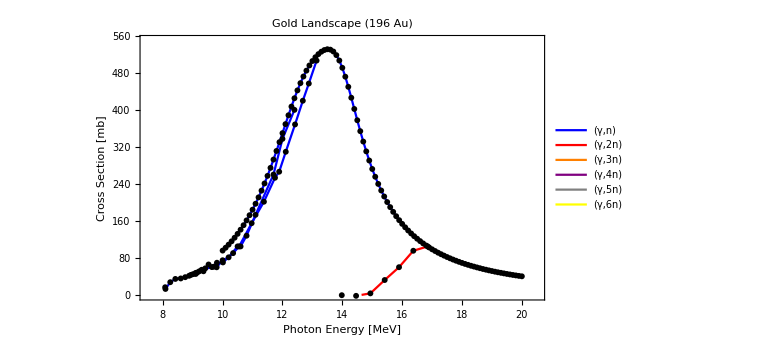

```mathematica
ListPlot[{Partition[Riffle[Plaisir197Au196Au⟦All,1⟧,Plaisir197Au196Au⟦All,2⟧],2],Partition[Riffle[Plaisir197Au196Au⟦All,1⟧,Plaisir197Au196Au⟦All,2⟧],2],Partition[Riffle[Itoh197Au196Au⟦All,1⟧,Itoh197Au196Au⟦All,2⟧],2],Partition[Riffle[Itoh197Au196Au⟦All,1⟧,Itoh197Au196Au⟦All,2⟧],2],Partition[Riffle[Kitatani197Au196Au⟦All,1⟧,Kitatani197Au196Au⟦All,3⟧],2],Partition[Riffle[Kitatani197Au196Au⟦All,1⟧,Kitatani197Au196Au⟦All,3⟧],2],Partition[Riffle[Naik197Au195Au⟦All,1⟧,Naik197Au195Au⟦All,2⟧],2],Partition[Riffle[Naik197Au195Au⟦All,1⟧,Naik197Au195Au⟦All,2⟧],2],Partition[Riffle[Berman197Au195Au⟦All,1⟧,Berman197Au195Au⟦All,2⟧],2],Partition[Riffle[Berman197Au195Au⟦All,1⟧,Berman197Au195Au⟦All,2⟧],2],Partition[Riffle[Naik197Au194Au⟦All,1⟧,Naik197Au194Au⟦All,2⟧],2],Partition[Riffle[Naik197Au194Au⟦All,1⟧,Naik197Au194Au⟦All,2⟧],2],Partition[Riffle[Veyissiere197Au194Au⟦All,1⟧,Veyissiere197Au194Au⟦All,2⟧],2],Partition[Riffle[Veyissiere197Au194Au⟦All,1⟧,Veyissiere197Au194Au⟦All,2⟧],2],Partition[Riffle[Naik197Au193Au⟦All,1⟧,Naik197Au193Au⟦All,2⟧],2],Partition[Riffle[Naik197Au193Au⟦All,1⟧,Naik197Au193Au⟦All,2⟧],2],Partition[Riffle[Naik197Au192Au⟦All,1⟧,Naik197Au192Au⟦All,2⟧],2],Partition[Riffle[Naik197Au192Au⟦All,1⟧,Naik197Au192Au⟦All,2⟧],2],Partition[Riffle[Naik197Au191Au⟦All,1⟧,Naik197Au191Au⟦All,2⟧],2],Partition[Riffle[Naik197Au191Au⟦All,1⟧,Naik197Au191Au⟦All,2⟧],2]},PlotStyle->{Black,Blue,Black,Blue,Black,Blue,Black,Red,Black,Red,Black,Orange,Black,Orange,Black,Purple,Black,Gray,Black,Yellow},Joined->{False,True},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"Gold Landscape (196 Au)",LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{None,"(γ,n)",None,None,None,None,None,"(γ,2n)",None,None,None,"(γ,3n)",None,None,None,"(γ,4n)",None,"(γ,5n)",None,"(γ,6n)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.75}],PlotRange->{{7.5,20.5},{0,550}},ImageSize->Large]
```

## Zirconium 89 Investigation + Yttrium 89 (γ,p) route

Notes
• Zirconium Iostopes can’t be separated by a centrifuge as there is no volatile compound - at least in 1956. Can be separated by SILEX, papers on this.
• Cyclotron production of Zr 89 is possible and is already exploited, I think. What are these production routes?
• There are lots of possible isotopes of Zr, therefore lots of disruptor processes are possible.
• Zr 90 is 51.45% abundant.
• The simple Zr 90 photonuclear reaction (γ,n) seems to favour ending in an excited “m” state. Is this usable?
• The Zr 90 → Zr 89 (γ,n) reaction had incorrect units in the EXFOR database.
• The other production methods of Zr 89 from (γ,α) and (γ,p) seem to be from unstable isotopes.
• The other disruptor routes for Zr 89 are:
	• Zr 90 (γ,p) which coincides with excited state peak.
	• Zr 90 (γ,α) has poor data + seems small.
	• Zr 90 (γ,2+p) has no data.
	• Zr 91, 94, 96 (γ,1+p) has no data, Zr 92 (γ,1+p) has poor data.
	• Zr 96 (γ,n) data is poorly understood.
	• Zr 96 (γ,α) data is available. The rest of the isotopes (γ,α) reactions have no data.

```mathematica
SetDirectory[NotebookDirectory[]];
BanuZr90Zr89 =Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/90Zr (g,n)/Banu_90Zr_to_89Zr.txt","Table"],2];

BrajnikZr90Zr89m =Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/90Zr (g,n)/Brajnik_90Zr_to_89mZr.txt","Table"],2];
MutsuroZr90Zr89m =Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/90Zr (g,n)/Mutsuro_90Zr_to_89mZr.txt","Table"],2];

BrajnikZr90Zr88=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/90Zr (g,2n)/Brajnik_90Zr_to_88Zr.txt","Table"],2];
LepretreZr90Zr88=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/90Zr (g,2n)/Lepretre_90Zr_to_88Zr.txt","Table"],2];

BrajnikZr90Y89=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/90Zr (g,p)/Brajnik_90Zr_to_89Y.txt","Table"],2];

GoryachevZr91Zr90=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/91Zr (g,n)/Goryachev_91Zr_to_90Zr.txt","Table"],2];
UtsunomiyaZr91Zr90=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/91Zr (g,n)/Utsunomiya_91Zr_to_90Zr.txt","Table"],2];

UtsunomiyaZr92Zr91=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/92Zr (g,n)/Utsunomiya_92Zr_to_91Zr.txt","Table"],2];

UtsunomiyaZr94Zr93=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/94Zr (g,n)/Utsunomiya_94Zr_to_93Zr.txt","Table"],2];

AntonovZr96Sr92=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Zirconium89/96Zr (g,a)/Antonov_96Zr_to_92Sr.txt","Table"],2];
```

## 90 Zr → 89 Zr (γ,n)

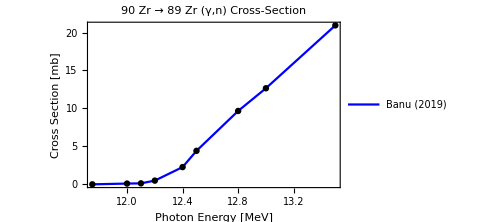

```mathematica
ListPlot[{Partition[Riffle[BanuZr90Zr89⟦All,1⟧,BanuZr90Zr89⟦All,3⟧],2],Partition[Riffle[BanuZr90Zr89⟦All,1⟧,BanuZr90Zr89⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"90 Zr → 89 Zr (γ,n) Cross-Section",PlotLegends->Placed[LineLegend[{None,"Banu (2019)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.6}],ImageSize->Medium]
```

## 90 Zr → 89m Zr (γ,n)

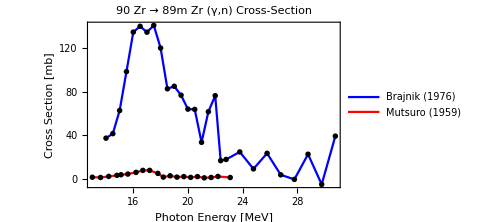

```mathematica
ListPlot[{Partition[Riffle[BrajnikZr90Zr89m⟦All,1⟧,BrajnikZr90Zr89m⟦All,2⟧],2],Partition[Riffle[BrajnikZr90Zr89m⟦All,1⟧,BrajnikZr90Zr89m⟦All,2⟧],2],Partition[Riffle[MutsuroZr90Zr89m⟦All,1⟧,MutsuroZr90Zr89m⟦All,2⟧],2],Partition[Riffle[MutsuroZr90Zr89m⟦All,1⟧,MutsuroZr90Zr89m⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"90 Zr → 89m Zr (γ,n) Cross-Section",PlotLegends->Placed[LineLegend[{None,"Brajnik (1976)",None,"Mutsuro (1959)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.77,0.7}],ImageSize->Medium]
```

## 90 Zr → 88 Zr (γ,2n)

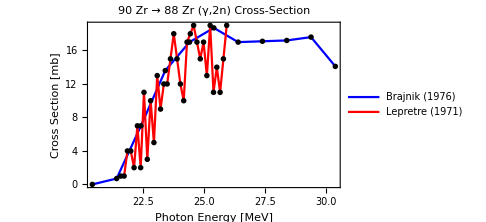

```mathematica
ListPlot[{Partition[Riffle[BrajnikZr90Zr88⟦All,1⟧,BrajnikZr90Zr88⟦All,2⟧],2],Partition[Riffle[BrajnikZr90Zr88⟦All,1⟧,BrajnikZr90Zr88⟦All,2⟧],2],Partition[Riffle[LepretreZr90Zr88⟦All,1⟧,LepretreZr90Zr88⟦All,2⟧],2],Partition[Riffle[LepretreZr90Zr88⟦All,1⟧,LepretreZr90Zr88⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"90 Zr → 88 Zr (γ,2n) Cross-Section",PlotLegends->Placed[LineLegend[{None,"Brajnik (1976)",None,"Lepretre (1971)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.7,0.25}],ImageSize->Medium]
```

## 90 Zr → 89 Zr (γ,p)

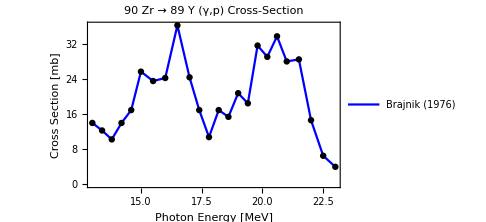

```mathematica
ListPlot[{Partition[Riffle[BrajnikZr90Y89⟦All,1⟧,BrajnikZr90Y89⟦All,2⟧],2],Partition[Riffle[BrajnikZr90Y89⟦All,1⟧,BrajnikZr90Y89⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"90 Zr → 89 Y (γ,p) Cross-Section",PlotLegends->Placed[LineLegend[{None,"Brajnik (1976)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.7,0.25}],ImageSize->Medium]
```

## 91 Zr → 90 Zr (γ,n)

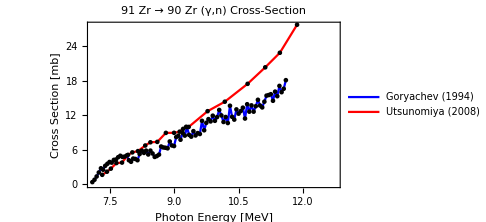

```mathematica
ListPlot[{Partition[Riffle[GoryachevZr91Zr90⟦All,1⟧,GoryachevZr91Zr90⟦All,2⟧],2],Partition[Riffle[GoryachevZr91Zr90⟦All,1⟧,GoryachevZr91Zr90⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr91Zr90⟦All,1⟧,UtsunomiyaZr91Zr90⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr91Zr90⟦All,1⟧,UtsunomiyaZr91Zr90⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"91 Zr → 90 Zr (γ,n) Cross-Section",PlotLegends->Placed[LineLegend[{None,"Goryachev (1994)",None,"Utsunomiya (2008)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.75}],ImageSize->Medium]
```

## 92 Zr → 91 Zr (γ,n)

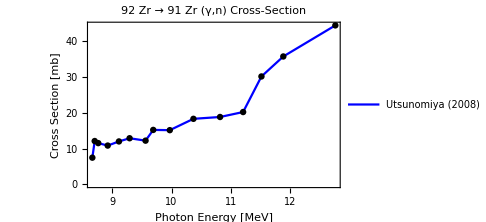

```mathematica
ListPlot[{Partition[Riffle[UtsunomiyaZr92Zr91⟦All,1⟧,UtsunomiyaZr92Zr91⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr92Zr91⟦All,1⟧,UtsunomiyaZr92Zr91⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"92 Zr → 91 Zr (γ,n) Cross-Section",PlotLegends->Placed[LineLegend[{None,"Utsunomiya (2008)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.6}],ImageSize->Medium]
```

## 94 Zr → 93 Zr (γ,n)

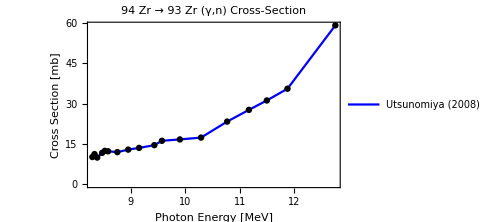

```mathematica
ListPlot[{Partition[Riffle[UtsunomiyaZr94Zr93⟦All,1⟧,UtsunomiyaZr94Zr93⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr94Zr93⟦All,1⟧,UtsunomiyaZr94Zr93⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"94 Zr → 93 Zr (γ,n) Cross-Section",PlotLegends->Placed[LineLegend[{None,"Utsunomiya (2008)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.6}],ImageSize->Medium]
```

## 96 Zr → 92 Sr (γ,α)

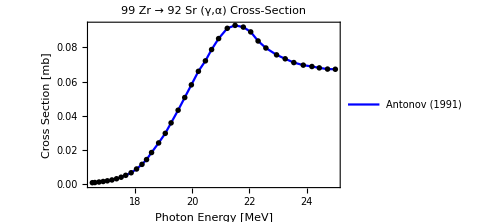

```mathematica
ListPlot[{Partition[Riffle[AntonovZr96Sr92⟦All,1⟧,AntonovZr96Sr92⟦All,2⟧],2],Partition[Riffle[AntonovZr96Sr92⟦All,1⟧,AntonovZr96Sr92⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},PlotLabel->"99 Zr → 92 Sr (γ,α) Cross-Section",PlotLegends->Placed[LineLegend[{None,"Antonov (1991)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.3}],ImageSize->Medium]
```

## Zirconium Photonuclear Landscape (Zr 89)

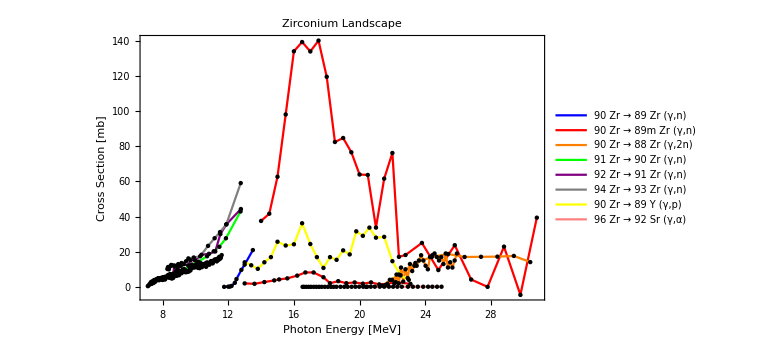

```mathematica
ListPlot[{Partition[Riffle[BanuZr90Zr89⟦All,1⟧,BanuZr90Zr89⟦All,3⟧],2],Partition[Riffle[BanuZr90Zr89⟦All,1⟧,BanuZr90Zr89⟦All,3⟧],2],Partition[Riffle[BrajnikZr90Zr89m⟦All,1⟧,BrajnikZr90Zr89m⟦All,2⟧],2],Partition[Riffle[BrajnikZr90Zr89m⟦All,1⟧,BrajnikZr90Zr89m⟦All,2⟧],2],Partition[Riffle[MutsuroZr90Zr89m⟦All,1⟧,MutsuroZr90Zr89m⟦All,2⟧],2],Partition[Riffle[MutsuroZr90Zr89m⟦All,1⟧,MutsuroZr90Zr89m⟦All,2⟧],2],Partition[Riffle[BrajnikZr90Zr88⟦All,1⟧,BrajnikZr90Zr88⟦All,2⟧],2],Partition[Riffle[BrajnikZr90Zr88⟦All,1⟧,BrajnikZr90Zr88⟦All,2⟧],2],Partition[Riffle[LepretreZr90Zr88⟦All,1⟧,LepretreZr90Zr88⟦All,2⟧],2],Partition[Riffle[LepretreZr90Zr88⟦All,1⟧,LepretreZr90Zr88⟦All,2⟧],2],Partition[Riffle[GoryachevZr91Zr90⟦All,1⟧,GoryachevZr91Zr90⟦All,2⟧],2],Partition[Riffle[GoryachevZr91Zr90⟦All,1⟧,GoryachevZr91Zr90⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr91Zr90⟦All,1⟧,UtsunomiyaZr91Zr90⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr91Zr90⟦All,1⟧,UtsunomiyaZr91Zr90⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr92Zr91⟦All,1⟧,UtsunomiyaZr92Zr91⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr92Zr91⟦All,1⟧,UtsunomiyaZr92Zr91⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr94Zr93⟦All,1⟧,UtsunomiyaZr94Zr93⟦All,2⟧],2],Partition[Riffle[UtsunomiyaZr94Zr93⟦All,1⟧,UtsunomiyaZr94Zr93⟦All,2⟧],2],Partition[Riffle[BrajnikZr90Y89⟦All,1⟧,BrajnikZr90Y89⟦All,2⟧],2],Partition[Riffle[BrajnikZr90Y89⟦All,1⟧,BrajnikZr90Y89⟦All,2⟧],2],Partition[Riffle[AntonovZr96Sr92⟦All,1⟧,AntonovZr96Sr92⟦All,2⟧],2],Partition[Riffle[AntonovZr96Sr92⟦All,1⟧,AntonovZr96Sr92⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red,Black,Red,Black,Orange,Black,Orange,Black,Green,Black,Green,Black,Purple,Black,Gray,Black,Yellow,Black,Pink},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{18,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{None,"90 Zr → 89 Zr (γ,n)",None,"90 Zr → 89m Zr (γ,n)",None,None,None,"90 Zr → 88 Zr (γ,2n)",None,None,None,"91 Zr → 90 Zr (γ,n)",None,None,None,"92 Zr → 91 Zr (γ,n)",None,"94 Zr → 93 Zr (γ,n)",None,"90 Zr → 89 Y (γ,p)",None,"96 Zr → 92 Sr (γ,α)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.85,0.7}],PlotLabel->"Zirconium Landscape",PlotRange->All,ImageSize->Large]
```

## Titanium 45 Investigation

Notes
• Titanium 46 can be separated by using a centrifuge with TiCl_4.
• Cyclotron production of Ti 45 is possible. 45 Sc → 45 Ti (p,n).
• Titanium 45 is primarily used for PET imaging.  
• 45 Ti decays by β^+ emission t_(1/2) ~ 3h.
• Very limited cross section data for Titanium.
• Multiple Isotopes of Titanium abundant (46, 47, 48, 49)
• Other production methods (γ,p) and (γ,α) seem impossible due to instability of target isotopes required for these.
• The main photonuclear production route is:
	• 46 Ti → 45 Ti (γ,n)
• Possible disruptor routes are:
	• 47, 48, 48 Ti (γ,1+n) reactions, for which no data is available.
	• 46 Ti (γ,2+n) has no data.
	• No available data or poor ratio data for Ti (γ,p) reactions.
	• No available data for Ti (γ,α) reactions.

```mathematica
SetDirectory[NotebookDirectory[]];
PywellTi46Ti45 =Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Titanium45/46Ti (g,n)/Pywell_46Ti_to_45Ti.txt","Table"],2];
```

## 46 Ti → 45 Ti (γ,n)

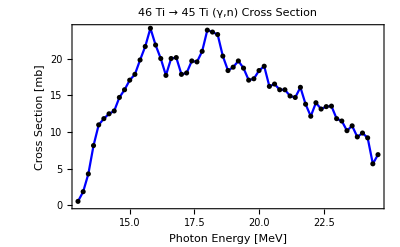

```mathematica
ListPlot[{Partition[Riffle[PywellTi46Ti45⟦All,1⟧,PywellTi46Ti45⟦All,2⟧],2],Partition[Riffle[PywellTi46Ti45⟦All,1⟧,PywellTi46Ti45⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"46 Ti → 45 Ti (γ,n) Cross Section"]
```

No useful data on other Titanium isotopes.

## Copper 64 Investigation

Notes
• Copper 64 cyclotron production is possible. 64 Ni → 64 Cu (p,n) route.
• Copper isotopes can’t be separated by centrifuge (at least not in 1956) as there is no volatile compound. Chromatographic and ion-exchange methods are possible.
• Only 63 Cu and 65 Cu are stable. 65 Cu is less abundant ~30.83%.
• Copper 64 is a popular PET isotope. It is a β^+ (61%) and β^- (39%) emitter with t_(1/2) = 12.7 h/.
• The main photonuclear route for 64 Cu is:
	• 65 Cu → 64 Cu (γ,n) 
• Other photo-production routes include:
	• 66 Zn (γ,p+n) which there is no data for.
	• 68 Ga (γ,α) is not stable.
• Potential disruptor routes unconsidered are:
	• 65 Cu (γ,1+p) which there is no data for. May overlap.
	• 65 Cu (γ,2+n) which there is no data for, probably much higher energy.
	• 63 Cu (γ,3+n) which there is no data for but is probably high energy
	• 63 Cu (γ,α) has no data, probably a small effect.

```mathematica
SetDirectory[NotebookDirectory[]];
AntonovCu65Cu64 =Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Copper64/65Cu (g,n)/Antonov_65Cu_to_64Cu.txt","Table"],2];
KatzCu65Cu64 =Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Copper64/65Cu (g,n)/Katz_65Cu_to_64Cu.txt","Table"],2];

AntonovCu65Co61=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Copper64/65Cu (g,a)/Antonov_65Cu_to_61Co.txt","Table"],2];

PlasnirCu63Cu62=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Copper64/63Cu (g,n)/Plasnir_63Cu_to_62Cu.txt","Table"],2];
DzhilavyanCu63Cu62=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Copper64/63Cu (g,n)/Dzhilavyan_63Cu_to_62Cu.txt","Table"],2];
SundCu63Cu62=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Copper64/63Cu (g,n)/Sund_63Cu_to_62Cu.txt","Table"],2];

AntunesCu63Cu61=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Copper64/63Cu (g,2n)/Antunes_63Cu_to_61Cu.txt","Table"],2];
BermanCu63Cu61=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Copper64/63Cu (g,2n)/Berman_63Cu_to_61Cu.txt","Table"],2];
SundCu63Cu61=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Copper64/63Cu (g,2n)/Sund_63Cu_to_61Cu.txt","Table"],2];
```

## 65 Cu → 64 Cu (γ,n)

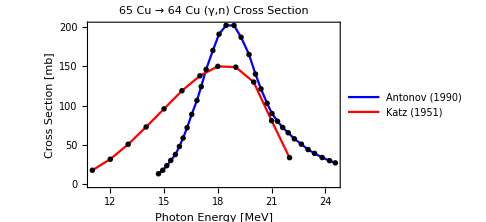

```mathematica
ListPlot[{Partition[Riffle[AntonovCu65Cu64⟦All,1⟧,AntonovCu65Cu64⟦All,2⟧],2],Partition[Riffle[AntonovCu65Cu64⟦All,1⟧,AntonovCu65Cu64⟦All,2⟧],2],Partition[Riffle[KatzCu65Cu64⟦All,1⟧,KatzCu65Cu64⟦All,2⟧],2],Partition[Riffle[KatzCu65Cu64⟦All,1⟧,KatzCu65Cu64⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"65 Cu → 64 Cu (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Antonov (1990)",None,"Katz (1951)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.22,0.82}],ImageSize->Medium]
```

## 65 Cu → 61 C0 (γ,α)

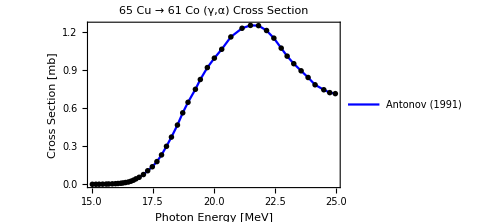

```mathematica
ListPlot[{Partition[Riffle[AntonovCu65Co61⟦All,1⟧,AntonovCu65Co61⟦All,2⟧],2],Partition[Riffle[AntonovCu65Co61⟦All,1⟧,AntonovCu65Co61⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"65 Cu → 61 Co (γ,α) Cross Section",PlotLegends->Placed[LineLegend[{None,"Antonov (1991)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.22,0.82}],ImageSize->Medium]
```

## 63 Cu → 62 Cu (γ,n)

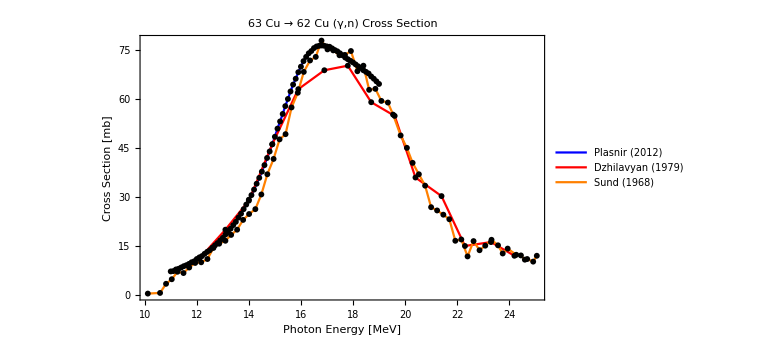

```mathematica
ListPlot[{Partition[Riffle[PlasnirCu63Cu62⟦All,1⟧,PlasnirCu63Cu62⟦All,2⟧],2],Partition[Riffle[PlasnirCu63Cu62⟦All,1⟧,PlasnirCu63Cu62⟦All,2⟧],2],Partition[Riffle[DzhilavyanCu63Cu62⟦All,1⟧,DzhilavyanCu63Cu62⟦All,2⟧],2],Partition[Riffle[DzhilavyanCu63Cu62⟦All,1⟧,DzhilavyanCu63Cu62⟦All,2⟧],2],Partition[Riffle[SundCu63Cu62⟦All,1⟧,SundCu63Cu62⟦All,2⟧],2],Partition[Riffle[SundCu63Cu62⟦All,1⟧,SundCu63Cu62⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red,Black,Orange},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"63 Cu → 62 Cu (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Plasnir (2012)",None,"Dzhilavyan (1979)",None,"Sund (1968)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.2}],ImageSize->Large]
```

## 63 Cu → 61 Cu (γ,2n)

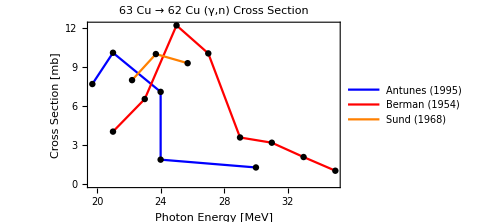

```mathematica
ListPlot[{Partition[Riffle[AntunesCu63Cu61⟦All,1⟧,AntunesCu63Cu61⟦All,3⟧],2],Partition[Riffle[AntunesCu63Cu61⟦All,1⟧,AntunesCu63Cu61⟦All,3⟧],2],Partition[Riffle[BermanCu63Cu61⟦All,1⟧,BermanCu63Cu61⟦All,2⟧],2],Partition[Riffle[BermanCu63Cu61⟦All,1⟧,BermanCu63Cu61⟦All,2⟧],2],Partition[Riffle[SundCu63Cu61⟦All,1⟧,SundCu63Cu61⟦All,2⟧],2],Partition[Riffle[SundCu63Cu61⟦All,1⟧,SundCu63Cu61⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red,Black,Orange},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"63 Cu → 62 Cu (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Antunes (1995)",None,"Berman (1954)",None,"Sund (1968)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.5}],ImageSize->Medium]
```

## Copper Photonuclear Landscape

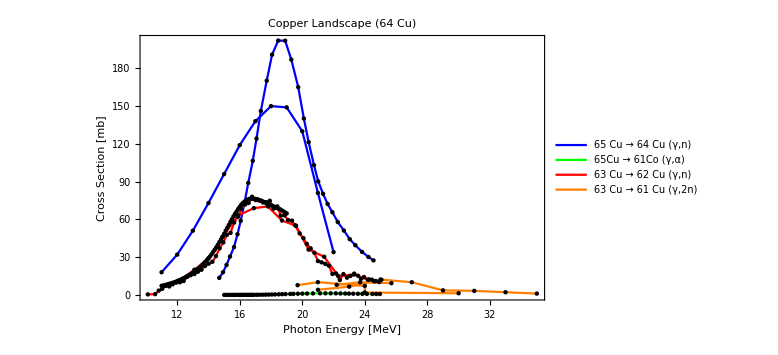

```mathematica
ListPlot[{Partition[Riffle[AntonovCu65Cu64⟦All,1⟧,AntonovCu65Cu64⟦All,2⟧],2],Partition[Riffle[AntonovCu65Cu64⟦All,1⟧,AntonovCu65Cu64⟦All,2⟧],2],Partition[Riffle[KatzCu65Cu64⟦All,1⟧,KatzCu65Cu64⟦All,2⟧],2],Partition[Riffle[KatzCu65Cu64⟦All,1⟧,KatzCu65Cu64⟦All,2⟧],2],Partition[Riffle[AntonovCu65Co61⟦All,1⟧,AntonovCu65Co61⟦All,2⟧],2],Partition[Riffle[AntonovCu65Co61⟦All,1⟧,AntonovCu65Co61⟦All,2⟧],2],Partition[Riffle[PlasnirCu63Cu62⟦All,1⟧,PlasnirCu63Cu62⟦All,2⟧],2],Partition[Riffle[PlasnirCu63Cu62⟦All,1⟧,PlasnirCu63Cu62⟦All,2⟧],2],Partition[Riffle[DzhilavyanCu63Cu62⟦All,1⟧,DzhilavyanCu63Cu62⟦All,2⟧],2],Partition[Riffle[DzhilavyanCu63Cu62⟦All,1⟧,DzhilavyanCu63Cu62⟦All,2⟧],2],Partition[Riffle[SundCu63Cu62⟦All,1⟧,SundCu63Cu62⟦All,2⟧],2],Partition[Riffle[SundCu63Cu62⟦All,1⟧,SundCu63Cu62⟦All,2⟧],2],Partition[Riffle[AntunesCu63Cu61⟦All,1⟧,AntunesCu63Cu61⟦All,3⟧],2],Partition[Riffle[AntunesCu63Cu61⟦All,1⟧,AntunesCu63Cu61⟦All,3⟧],2],Partition[Riffle[BermanCu63Cu61⟦All,1⟧,BermanCu63Cu61⟦All,2⟧],2],Partition[Riffle[BermanCu63Cu61⟦All,1⟧,BermanCu63Cu61⟦All,2⟧],2],Partition[Riffle[SundCu63Cu61⟦All,1⟧,SundCu63Cu61⟦All,2⟧],2],Partition[Riffle[SundCu63Cu61⟦All,1⟧,SundCu63Cu61⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Blue,Black,Green,Black,Red,Black,Red,Black,Red,Black,Orange,Black,Orange,Black,Orange},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{18,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{None,"65 Cu → 64 Cu (γ,n)",None,None,None,"65Cu → 61Co (γ,α)",None,"63 Cu → 62 Cu (γ,n)",None,None,None,None,None,"63 Cu → 61 Cu (γ,2n)",None,None,None,None},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.7}],PlotLabel->"Copper Landscape (64 Cu)",PlotRange->All,ImageSize->Large]
```

## Caesium 132 + 131 Investigation [Add Disruptors]

Notes
Caesium 132 and 131 production seem to be closely linked. They appear to be a Theranostic pair. Both can be produced using 133 Cs from (γ,n) and (γ,2n) photo-nuclear reactions. These have accompanying (γ,n+p), (γ,2n+p) disruptor routes which produce stable Xenon isotopes (131 Xe and 130 Xe). If possible to separate the Xenon and the Caesium, then these could possibly be produced via a 2 - energy (double laser cavity/ double IP/multi-colour) ICS source - which would be a very cool use! 

• The Cs 133 (γ,n) average cross section data is 0.1032 barns for an energy range of 8.987 → 32 MeV.
• Cs 133 is the mono-stable isotope of Caesium so would be a good target material.
• Medical usage of Cs 132 not well known or investigated from what I can see. Appears to be a PET or SPECT isotope. Theranostic with 131 Cs?
• Medical usage of Cs 131 appears to be for Brachytherapy and potentially imaging uses (more historic it seems).
• Cs 132 is a β^+ (98%) and β^- (2%) emitter with a half life t_(1/2) = 6.48 days. 
• Cs 131 decays by electron capture solely, t_(1/2) = 9.69 days.
• The main photonuclear route to 132 Cs is:
	• 133 Cs → 132 Cs (γ,n)
• The main photonuclear route to 131 Cs is:
	• 133 Cs → 131 Cs (γ,2n)
• Data is available for the 133 Cs (γ,n) → 132 Cs + 133 Cs (γ,n+p) → 131 Xe reaction combined. The (γ,n+p) reaction has a threshold at 15 MeV. 
• Data is available for the 133 Cs (γ,2n) → 131 Cs + 133 Cs (γ,2n+p) → 130 Xe reaction combined. The (γ,2n+p) reaction has a threshold at 21.6 MeV. 
• The cross section 133 Cs (γ,n) 132 Cs seems to peak ~ 15 MeV so can maybe run just under (γ,n+p) threshold for ‘clean’ production.  
• Other possible production routes are:
	• 135 La (γ,α) which is unstable.
	• 136 La (γ,α) which is unstable.
	• 132 Ba (γ,p) has no data.
	• 134 Ba (γ,p+n) has no data.
• Possible disruptor routes are:
	• 133 Cs (γ,4+n) which is likely to be in a much higher energy range.
	• 133 Cs (γ,1+p) which there is no data on.
	• 133 Cs (γ,α) which there is no data on, but is likely to have a very small cross section.
	
	NEED TO ADD ON DISRUPTORS I HAVE FOUND! UP TO 3n ROUTES

```mathematica
SetDirectory[NotebookDirectory[]];
Berman133Cs132Cs=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Caesium132/133Cs (g,n)/Berman_133Cs_to_132Cs.txt","Table"],2];
Lepretre133Cs132Cs=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Caesium132/133Cs (g,n)/Lepretre_133Cs_to_132Cs.txt","Table"],2];

Berman133Cs132Cs131Xe=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Caesium132/133Cs (g,np)/Berman_133Cs_to_132Cs131Xe.txt","Table"],2];
Lepretre133Cs132Cs131Xe=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Caesium132/133Cs (g,np)/Lepretre_133Cs_to_132Cs131Xe.txt","Table"],2];
```

```mathematica
Rahman133Cs132Cs={{8.987,103.2},{32,103.2}};
Rahman133Cs132Cs15={{8.987,103.2},{15,103.2}};

Berman133Cs131Cs=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Caesium132/133Cs (g,2n)/Berman_133Cs_to_131Cs.txt","Table"],2];
Lepretre133Cs131Cs=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Caesium132/133Cs (g,2n)/Lepretre_133Cs_to_131Cs.txt","Table"],2];

Berman133Cs131Cs130Xe=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Caesium132/133Cs (g,2np)/Berman_133Cs_to_131Cs130Xe.txt","Table"],2];
Lepretre133Cs131Cs130Xe=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Caesium132/133Cs (g,2np)/Lepretre_133Cs_to_131Cs130Xe.txt","Table"],2];

Berman133Cs130Cs=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Caesium132/133Cs (g,3n)/Berman_133Cs_to_130Cs.txt","Table"],2];
```

## Partial 133 Cs → 132 Cs (γ,n)

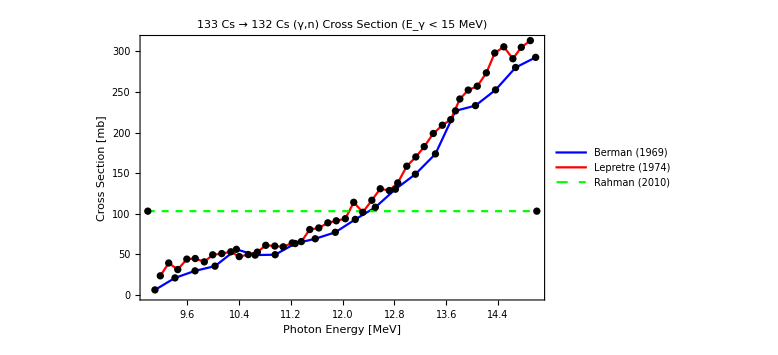

```mathematica
ListPlot[{Partition[Riffle[Berman133Cs132Cs⟦All,1⟧,Berman133Cs132Cs⟦All,2⟧],2],Partition[Riffle[Berman133Cs132Cs⟦All,1⟧,Berman133Cs132Cs⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs132Cs⟦All,1⟧,Lepretre133Cs132Cs⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs132Cs⟦All,1⟧,Lepretre133Cs132Cs⟦All,2⟧],2],Rahman133Cs132Cs15,Rahman133Cs132Cs15},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red,Black,{Green,Dashed}},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"133 Cs → 132 Cs (γ,n) Cross Section (E_γ < 15 MeV)",PlotLegends->Placed[LineLegend[{None,"Berman (1969)",None,"Lepretre (1974)",None,"Rahman (2010)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.22,0.82}],ImageSize->Large]
```

## 133 Cs → 132 Cs (γ,n) + 131 Xe (γ,n+p)

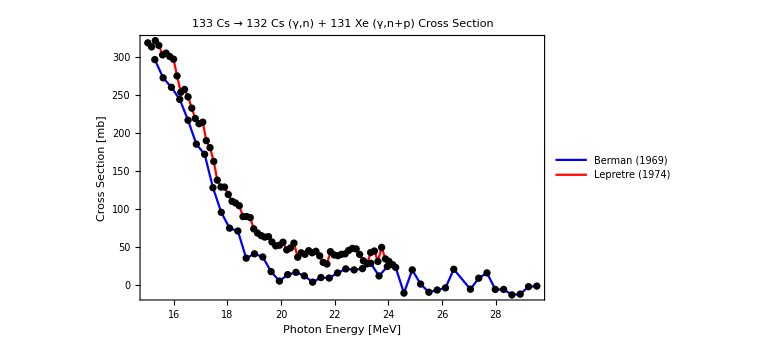

```mathematica
ListPlot[{Partition[Riffle[Berman133Cs132Cs131Xe⟦All,1⟧,Berman133Cs132Cs131Xe⟦All,2⟧],2],Partition[Riffle[Berman133Cs132Cs131Xe⟦All,1⟧,Berman133Cs132Cs131Xe⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs132Cs131Xe⟦All,1⟧,Lepretre133Cs132Cs131Xe⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs132Cs131Xe⟦All,1⟧,Lepretre133Cs132Cs131Xe⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"133 Cs → 132 Cs (γ,n) + 131 Xe (γ,n+p) Cross Section",PlotLegends->Placed[LineLegend[{None,"Berman (1969)",None,"Lepretre (1974)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.82,0.82}],ImageSize->Large]
```

## Partial 133 Cs → 131 Cs (γ,n)

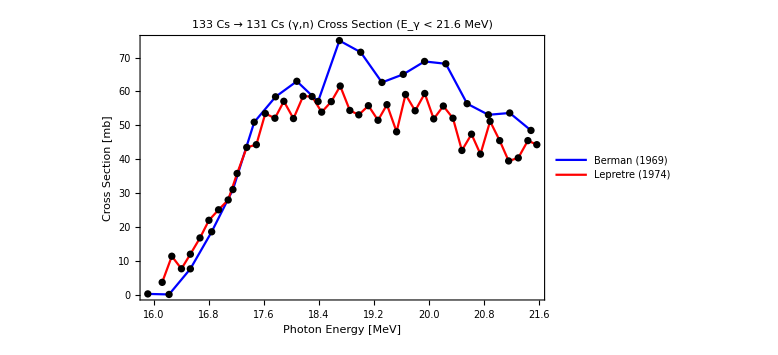

```mathematica
ListPlot[{Partition[Riffle[Berman133Cs131Cs⟦All,1⟧,Berman133Cs131Cs⟦All,2⟧],2],Partition[Riffle[Berman133Cs131Cs⟦All,1⟧,Berman133Cs131Cs⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs131Cs⟦All,1⟧,Lepretre133Cs131Cs⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs131Cs⟦All,1⟧,Lepretre133Cs131Cs⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"133 Cs → 131 Cs (γ,n) Cross Section (E_γ < 21.6 MeV)",PlotLegends->Placed[LineLegend[{None,"Berman (1969)",None,"Lepretre (1974)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.25}],ImageSize->Large]
```

## 133 Cs → 131 Cs (γ,n) + 130 Xe (γ,n+p)

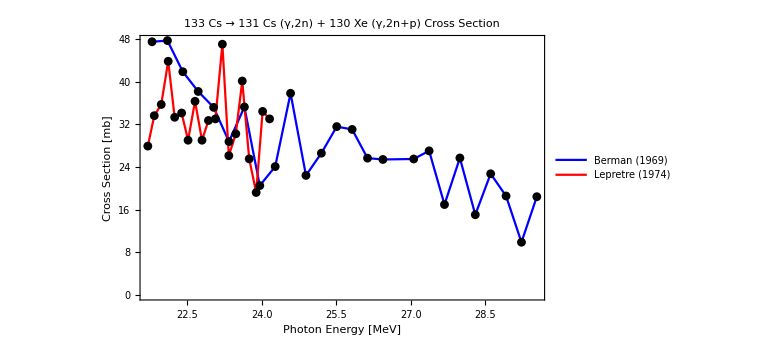

```mathematica
ListPlot[{Partition[Riffle[Berman133Cs131Cs130Xe⟦All,1⟧,Berman133Cs131Cs130Xe⟦All,2⟧],2],Partition[Riffle[Berman133Cs131Cs130Xe⟦All,1⟧,Berman133Cs131Cs130Xe⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs131Cs130Xe⟦All,1⟧,Lepretre133Cs131Cs130Xe⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs131Cs130Xe⟦All,1⟧,Lepretre133Cs131Cs130Xe⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"133 Cs → 131 Cs (γ,2n) + 130 Xe (γ,2n+p) Cross Section",PlotLegends->Placed[LineLegend[{None,"Berman (1969)",None,"Lepretre (1974)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.82,0.82}],ImageSize->Large]
```

## 133 Cs → 130 Cs (γ,3n)

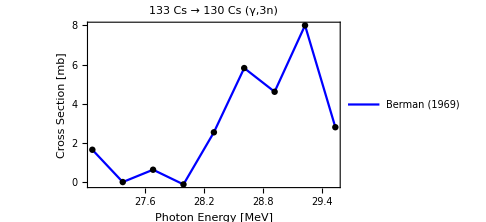

```mathematica
ListPlot[{Partition[Riffle[Berman133Cs130Cs⟦All,1⟧,Berman133Cs130Cs⟦All,2⟧],2],Partition[Riffle[Berman133Cs130Cs⟦All,1⟧,Berman133Cs130Cs⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"133 Cs → 130 Cs (γ,3n)",PlotLegends->Placed[LineLegend[{None,"Berman (1969)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.2}],ImageSize->Medium]
```

## Caesium Landscape

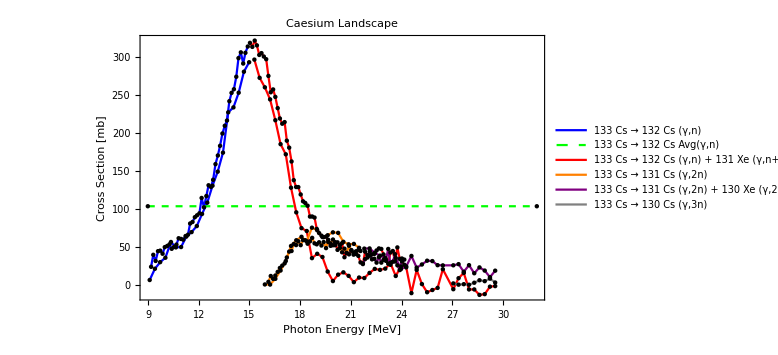

```mathematica
ListPlot[{Partition[Riffle[Berman133Cs132Cs⟦All,1⟧,Berman133Cs132Cs⟦All,2⟧],2],Partition[Riffle[Berman133Cs132Cs⟦All,1⟧,Berman133Cs132Cs⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs132Cs⟦All,1⟧,Lepretre133Cs132Cs⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs132Cs⟦All,1⟧,Lepretre133Cs132Cs⟦All,2⟧],2],Rahman133Cs132Cs,Rahman133Cs132Cs,Partition[Riffle[Berman133Cs132Cs131Xe⟦All,1⟧,Berman133Cs132Cs131Xe⟦All,2⟧],2],Partition[Riffle[Berman133Cs132Cs131Xe⟦All,1⟧,Berman133Cs132Cs131Xe⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs132Cs131Xe⟦All,1⟧,Lepretre133Cs132Cs131Xe⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs132Cs131Xe⟦All,1⟧,Lepretre133Cs132Cs131Xe⟦All,2⟧],2],Partition[Riffle[Berman133Cs131Cs⟦All,1⟧,Berman133Cs131Cs⟦All,2⟧],2],Partition[Riffle[Berman133Cs131Cs⟦All,1⟧,Berman133Cs131Cs⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs131Cs⟦All,1⟧,Lepretre133Cs131Cs⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs131Cs⟦All,1⟧,Lepretre133Cs131Cs⟦All,2⟧],2],Partition[Riffle[Berman133Cs131Cs130Xe⟦All,1⟧,Berman133Cs131Cs130Xe⟦All,2⟧],2],Partition[Riffle[Berman133Cs131Cs130Xe⟦All,1⟧,Berman133Cs131Cs130Xe⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs131Cs130Xe⟦All,1⟧,Lepretre133Cs131Cs130Xe⟦All,2⟧],2],Partition[Riffle[Lepretre133Cs131Cs130Xe⟦All,1⟧,Lepretre133Cs131Cs130Xe⟦All,2⟧],2],Partition[Riffle[Berman133Cs130Cs⟦All,1⟧,Berman133Cs130Cs⟦All,2⟧],2],Partition[Riffle[Berman133Cs130Cs⟦All,1⟧,Berman133Cs130Cs⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Blue,Black,{Green,Dashed},Black,Red,Black,Red,Black,Orange,Black,Orange,Black,Purple,Black,Purple,Black,Gray},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Caesium Landscape",PlotLegends->Placed[LineLegend[{None,"133 Cs → 132 Cs (γ,n)",None,None,None,"133 Cs → 132 Cs Avg(γ,n)",None,"133 Cs → 132 Cs (γ,n) + 131 Xe (γ,n+p)",None,None,None,"133 Cs → 131 Cs (γ,2n)",None,None,None,"133 Cs → 131 Cs (γ,2n) + 130 Xe (γ,2n+p)",None,None,None,"133 Cs → 130 Cs (γ,3n)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.72,0.77}],ImageSize->Large]
```

## Scandium 47 Investigation

Notes
• The Titanium route can use 48 Ti as this can be separated using TiCl_4 in a centrifuge.
• The Calcium route can use 48 Ca as this can be separated using ‘band chromatography’.
• The Vanadium route can use 51 V the 99.75% abundant isotope. 
• 47 Sc is a β^- emitter for targeted radiotherapy and forms Theranostic pairs with 43 & 44 Sc, which are PET tracers.
• There is a cyclotron production route for 47 Sc:
	• 48 Ti (p,2n) → 47 Sc.
• Possible photo-production routes:
	• 48 Ti → 47 Sc (γ,p) route. Tried in 1976 from natural Ti.
	• 48 Ca → 47 Ca (γ,n) → 47 Sc (β^- 100%) ‘generator’ route. 47 Ca t_(1/2)=4.54 days, 47 Sc t_(1/2)=3.35 days. Requires separation.
	• 51 V → 47 Sc (γ,α) route.
• Possible ‘disruptor’ routes are (not shown here as separable + numerous):  
	• All Ti isotope (γ,n), (γ,2+p), (γ,α) reactions.
	• All  Ca (γ,2+n), (γ,p), (γ,α) reactions.
	• All  50 V reactions and other 51 V reactions.

```mathematica
SetDirectory[NotebookDirectory[]];
OKeefe48Ca47Ca=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Scandium47/48Ca (g,n)/OKeefe_48Ca_to_47Ca.txt","Table"],2];
Tompkins48Ca47Ca=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Scandium47/48Ca (g,n)/Tompkins_48Ca_to_47Ca.txt","Table"],2];

Sherwood48Ti47Sc=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Scandium47/48Ti (g,nx)/Sherwood_48Ti_to_47Sc.txt","Table"],2];

(*Antonov 1(1991) 2(1990)*) 
Antonov151V47Sc=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Scandium47/51V (g,a)/Antonov1_51V_to_47Sc.txt","Table"],2];
Antonov251V47Sc=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Scandium47/51V (g,a)/Antonov2_51V_to_47Sc.txt","Table"],2];
```

## 48Ca → 47 Ca (γ,n)

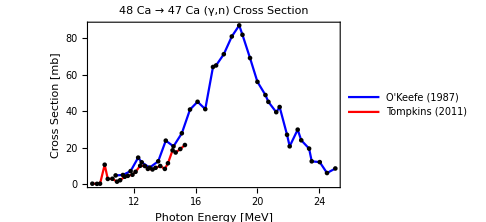

```mathematica
ListPlot[{Partition[Riffle[OKeefe48Ca47Ca⟦All,1⟧,OKeefe48Ca47Ca⟦All,2⟧],2],Partition[Riffle[OKeefe48Ca47Ca⟦All,1⟧,OKeefe48Ca47Ca⟦All,2⟧],2],Partition[Riffle[Tompkins48Ca47Ca⟦All,1⟧,Tompkins48Ca47Ca⟦All,2⟧],2],Partition[Riffle[Tompkins48Ca47Ca⟦All,1⟧,Tompkins48Ca47Ca⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"48 Ca → 47 Ca (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"O'Keefe (1987)",None,"Tompkins (2011)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.22,0.82}],ImageSize->Medium]
```

## nat Ti (~74% 48 Ti) → 47 Sc (γ,n) + (γ,X)

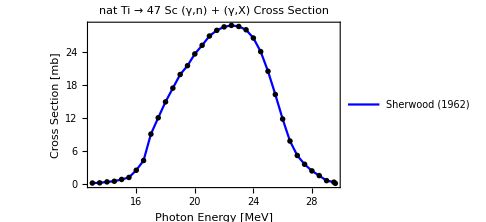

```mathematica
ListPlot[{Partition[Riffle[Sherwood48Ti47Sc⟦All,1⟧,Sherwood48Ti47Sc⟦All,2⟧],2],Partition[Riffle[Sherwood48Ti47Sc⟦All,1⟧,Sherwood48Ti47Sc⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"nat Ti → 47 Sc (γ,n) + (γ,X) Cross Section",PlotLegends->Placed[LineLegend[{None,"Sherwood (1962)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.22,0.82}],ImageSize->Medium]
```

## 51V → 47Sc (γ,α)

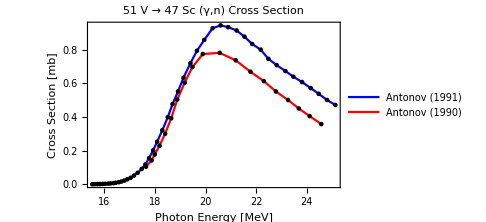

```mathematica
ListPlot[{Partition[Riffle[Antonov151V47Sc⟦All,1⟧,Antonov151V47Sc⟦All,2⟧],2],Partition[Riffle[Antonov151V47Sc⟦All,1⟧,Antonov151V47Sc⟦All,2⟧],2],Partition[Riffle[Antonov251V47Sc⟦All,1⟧,Antonov251V47Sc⟦All,2⟧],2],Partition[Riffle[Antonov251V47Sc⟦All,1⟧,Antonov251V47Sc⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"51 V → 47 Sc (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Antonov (1991)",None,"Antonov (1990)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.22,0.82}],ImageSize->Medium]
```

## 47 Scandium Photo-Nuclear Landscape

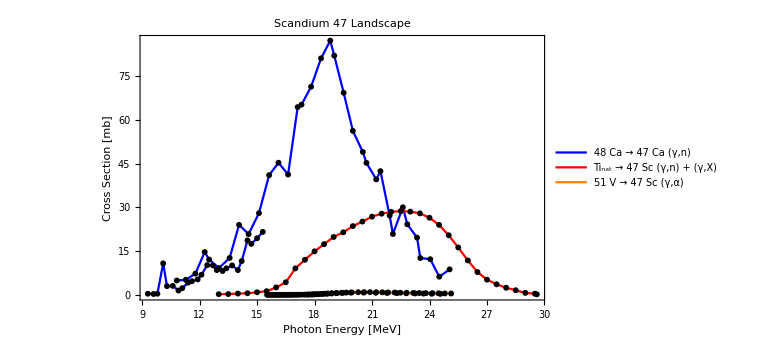

```mathematica
ListPlot[{Partition[Riffle[OKeefe48Ca47Ca⟦All,1⟧,OKeefe48Ca47Ca⟦All,2⟧],2],Partition[Riffle[OKeefe48Ca47Ca⟦All,1⟧,OKeefe48Ca47Ca⟦All,2⟧],2],Partition[Riffle[Tompkins48Ca47Ca⟦All,1⟧,Tompkins48Ca47Ca⟦All,2⟧],2],Partition[Riffle[Tompkins48Ca47Ca⟦All,1⟧,Tompkins48Ca47Ca⟦All,2⟧],2],Partition[Riffle[Sherwood48Ti47Sc⟦All,1⟧,Sherwood48Ti47Sc⟦All,2⟧],2],Partition[Riffle[Sherwood48Ti47Sc⟦All,1⟧,Sherwood48Ti47Sc⟦All,2⟧],2],Partition[Riffle[Antonov151V47Sc⟦All,1⟧,Antonov151V47Sc⟦All,2⟧],2],Partition[Riffle[Antonov151V47Sc⟦All,1⟧,Antonov151V47Sc⟦All,2⟧],2],Partition[Riffle[Antonov251V47Sc⟦All,1⟧,Antonov251V47Sc⟦All,2⟧],2],Partition[Riffle[Antonov251V47Sc⟦All,1⟧,Antonov251V47Sc⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Blue,Black,Red,Black,Orange,Black,Orange},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Scandium 47 Landscape",PlotLegends->Placed[LineLegend[{None,"48 Ca → 47 Ca (γ,n)",None,None,None," Ti_nat → 47 Sc (γ,n) + (γ,X)",None,"51 V → 47 Sc (γ,α)",None,None},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.82,0.82}],PlotRange->Full,ImageSize->Large]
```

## Iodine 126 Investigation

Notes
• Iodine 126 doesn’t seem to have a pertinent use. It is still listed on the isolpharm photo as a theranostic isotope. Need clarity on purpose!
• 126 I has t_(1/2)=12.9 days, it decays by β^- (47.3%) and β^+ (52.7%)
• Iodine 123 is used for thyroid imaging.
• Iodine 131 and 130 have been used for hyperthyroidism and thyroid cancer treatments.
• Production routes of 126 I are:
	• 127 I → 126 I (γ,n)
	• 128 Xe → 126 I (γ,p+n) with no data.
• Disruptor routes I have found for  126 I are:
	• 127 I → 125 Te (γ,n+p)
	• 127 I → 125 I (γ,2n)
	• 127 I → 12(3) I (γ,3+n) 3n not shown as too high energy, no data for 3+n.
	• 127 I (γ,1+p) no data

```mathematica
SetDirectory[NotebookDirectory[]];
Bergere127I126I=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iodine126/127I (g,n)/Bergere_127I_to_126I.txt","Table"],2];
Berman127I126I=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iodine126/127I (g,n)/Berman_127I_to_126I.txt","Table"],2];
Bramblett127I126I=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iodine126/127I (g,n)/Bramblett_127I_to_126I.txt","Table"],2];

Bergere127I126I125Te=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iodine126/127I (g,np)/Bergere_127I_to_126I125Te.txt","Table"],2];
Berman127I126I125Te=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iodine126/127I (g,np)/Berman_127I_to_126I125Te.txt","Table"],2];
Bramblett127I126I125Te=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iodine126/127I (g,np)/Bramblett_127I_to_126I125Te.txt","Table"],2];

Berman127I125I=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iodine126/127I (g,2n)/Berman_127I_to_125I.txt","Table"],2];
Rassol127I125I=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iodine126/127I (g,2n)/Rassol_127I_to_125I.txt","Table"],2];
```

## 127 I → 126 I (γ,n)

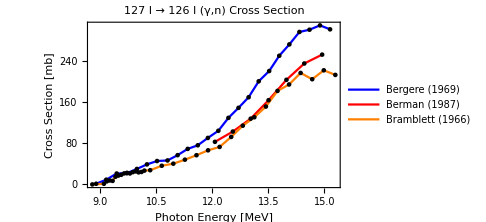

```mathematica
ListPlot[{Partition[Riffle[Bergere127I126I⟦All,1⟧,Bergere127I126I⟦All,2⟧],2],Partition[Riffle[Bergere127I126I⟦All,1⟧,Bergere127I126I⟦All,2⟧],2],Partition[Riffle[Berman127I126I⟦All,1⟧,Berman127I126I⟦All,2⟧],2],Partition[Riffle[Berman127I126I⟦All,1⟧,Berman127I126I⟦All,2⟧],2],Partition[Riffle[Bramblett127I126I⟦All,1⟧,Bramblett127I126I⟦All,2⟧],2],Partition[Riffle[Bramblett127I126I⟦All,1⟧,Bramblett127I126I⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red,Black,Orange},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"127 I → 126 I (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Bergere (1969)",None,"Berman (1987)",None,"Bramblett (1966)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.78}],ImageSize->Medium]
```

## 127 I → 126 I (γ,n) + 125 Te (γ,n+p)

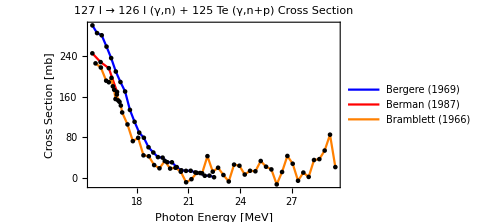

```mathematica
ListPlot[{Partition[Riffle[Bergere127I126I125Te⟦All,1⟧,Bergere127I126I125Te⟦All,2⟧],2],Partition[Riffle[Bergere127I126I125Te⟦All,1⟧,Bergere127I126I125Te⟦All,2⟧],2],Partition[Riffle[Berman127I126I125Te⟦All,1⟧,Berman127I126I125Te⟦All,2⟧],2],Partition[Riffle[Berman127I126I125Te⟦All,1⟧,Berman127I126I125Te⟦All,2⟧],2],Partition[Riffle[Bramblett127I126I125Te⟦All,1⟧,Bramblett127I126I125Te⟦All,2⟧],2],Partition[Riffle[Bramblett127I126I125Te⟦All,1⟧,Bramblett127I126I125Te⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red,Black,Orange},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"127 I → 126 I (γ,n) + 125 Te (γ,n+p) Cross Section",PlotLegends->Placed[LineLegend[{None,"Bergere (1969)",None,"Berman (1987)",None,"Bramblett (1966)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.72,0.75}],ImageSize->Medium]
```

## 127 I → 122 I (γ,2n)

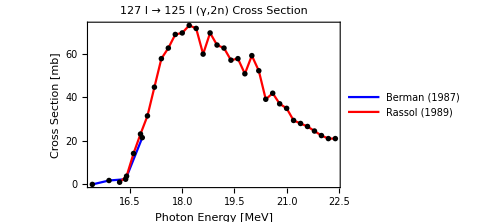

```mathematica
ListPlot[{Partition[Riffle[Berman127I125I⟦All,1⟧,Berman127I125I⟦All,2⟧],2],Partition[Riffle[Berman127I125I⟦All,1⟧,Berman127I125I⟦All,2⟧],2],Partition[Riffle[Rassol127I125I⟦All,1⟧,Rassol127I125I⟦All,2⟧],2],Partition[Riffle[Rassol127I125I⟦All,1⟧,Rassol127I125I⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"127 I → 125 I (γ,2n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Berman (1987)",None,"Rassol (1989)",None},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.2}],ImageSize->Medium]
```

## 126 Iodine Landscape

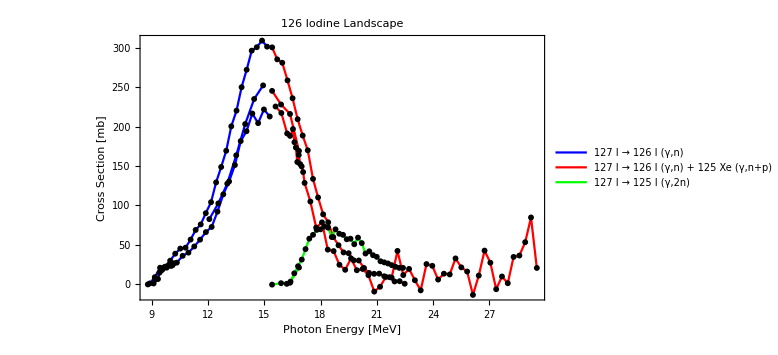

```mathematica
ListPlot[{Partition[Riffle[Bergere127I126I⟦All,1⟧,Bergere127I126I⟦All,2⟧],2],Partition[Riffle[Bergere127I126I⟦All,1⟧,Bergere127I126I⟦All,2⟧],2],Partition[Riffle[Berman127I126I⟦All,1⟧,Berman127I126I⟦All,2⟧],2],Partition[Riffle[Berman127I126I⟦All,1⟧,Berman127I126I⟦All,2⟧],2],Partition[Riffle[Bramblett127I126I⟦All,1⟧,Bramblett127I126I⟦All,2⟧],2],Partition[Riffle[Bramblett127I126I⟦All,1⟧,Bramblett127I126I⟦All,2⟧],2],Partition[Riffle[Bergere127I126I125Te⟦All,1⟧,Bergere127I126I125Te⟦All,2⟧],2],Partition[Riffle[Bergere127I126I125Te⟦All,1⟧,Bergere127I126I125Te⟦All,2⟧],2],Partition[Riffle[Berman127I126I125Te⟦All,1⟧,Berman127I126I125Te⟦All,2⟧],2],Partition[Riffle[Berman127I126I125Te⟦All,1⟧,Berman127I126I125Te⟦All,2⟧],2],Partition[Riffle[Bramblett127I126I125Te⟦All,1⟧,Bramblett127I126I125Te⟦All,2⟧],2],Partition[Riffle[Bramblett127I126I125Te⟦All,1⟧,Bramblett127I126I125Te⟦All,2⟧],2],Partition[Riffle[Berman127I125I⟦All,1⟧,Berman127I125I⟦All,2⟧],2],Partition[Riffle[Berman127I125I⟦All,1⟧,Berman127I125I⟦All,2⟧],2],Partition[Riffle[Rassol127I125I⟦All,1⟧,Rassol127I125I⟦All,2⟧],2],Partition[Riffle[Rassol127I125I⟦All,1⟧,Rassol127I125I⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Blue,Black,Blue,Black,Red,Black,Red,Black,Red,Black,Green,Black,Green},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"126 Iodine Landscape",PlotLegends->Placed[LineLegend[{None,"127 I → 126 I (γ,n)",None,None,None,None,None,"127 I → 126 I (γ,n) + 125 Xe (γ,n+p)",None,None,None,None,None,"127 I → 125 I (γ,2n)",None,None},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.7,0.78}],ImageSize->Large]
```

## Rhenium 186 Investigation

Notes
• 186 Re is used as a β^- emitter for treatment of bone metastases, radiosynovectomy, labelling of bombesin (tumor marker for small cell carcinoma of lung, gastric cancer, pancreatic cancer, and neuroblastoma), brachytherapy etc. It is a therapeutic isotope.
• 186 Re has t_(1/2)=3.72 days, it decays by β^- (92.53%) and EC (7.47%)
• Rhenium has 1 stable isotope 185 Re and 1 quasi-stable isotope 187 Re. Unusually, 187 Re - the quasi-stable isotope - is more abundant (62.6% vs 37.4%).
• Rhenium is a by-product of the extraction of Molybdenum and Copper ores. Primarily used in Jet Engine construction and as a Catalyst.
• Rhenium forms a hexafluoride ReF_6, which could theoretically be used in a centrifuge for isotopic separation.
• Production of 186 Re seems to be a current research area - 
• The main cyclotron production route for 186 Re is: 
	• 186 W → 186 Re (p,n) σ ~ 46 mb (v. small)
	• This also suffers from contamination from 185 W (p,n+p) (t_(1/2)=75.1 days) and 185 Re (p,2n) (stable) impurities.
	• Strangely, the (p,2n) cross section is dominant σ~857 mb (v. large)
	It seems that cyclotron production of 186 Rhenium is difficult...
• The main research reactor production rout for 186 Re is:
	• 185 Re → 186 Re (n,γ)
• The photonuclear production mechanisms are:
	• 187 Re → 186 Re (γ,n) - data seems like the cross section hasn’t peaked over energy range!
	• 187 Os → 186 Re (γ,p) no data. Osmium 187 is 1.6% abundant, many isotopes but forms hexafluoride OsF_6.
• The disruptor routes for a 187 Re target are:
	• 187 Re (γ,(1+)p) has no data
	• 187 Re (γ,(2+)n) has no data
	• 187 Re (γ,α) has no data
• The additional disruptor routes for a bulk Re target are:
	• 185 Re (γ,n) has only cross section ratio data.
	• 185 Re (γ,(2+)n) has no data
	• 185 Re (γ,(1+)p) has no data
	• 185 Re (γ,α)  has no data

```mathematica
SetDirectory[NotebookDirectory[]];
Shizuma187Re186Re=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Rhenium186/187Re (g,n)/Shizuma_187Re_to_186Re.txt","Table"],2];
```

## 187 Re → 186 Re (γ,n)

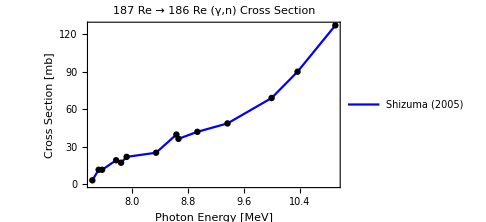

```mathematica
ListPlot[{Partition[Riffle[Shizuma187Re186Re⟦All,1⟧,Shizuma187Re186Re⟦All,2⟧],2],Partition[Riffle[Shizuma187Re186Re⟦All,1⟧,Shizuma187Re186Re⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"187 Re → 186 Re (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Shizuma (2005)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.78}],ImageSize->Medium]
```

## Iridium 192 Investigation

Notes
• 192 Ir is used as a β^- emitter for Brachytherapy, for implantation + therapeutic treatment for things such as skin cancer etc. Wires/ Pieces of metal typically irradiated + surgically inserted.
• 192 Ir has t_(1/2)=73.8 days, it decays by β^- (95.13%) and EC (4.87%)
• Iridium has 2 stable isotopes 191 Ir and 192 Ir. Abundance (37.3% vs 62.7%).
• Iridium forms a hexafluoride IrF_6, which could theoretically be used in a centrifuge for isotopic separation. 
• The main cyclotron production route for 192 Ir is: 
	• 192 Os → 192 Ir (p,n) 
	• This also suffers mainly contamination from 190 Ir  (t_(1/2)=11.78 days), 189 Ir  (t_(1/2)=13.19 days) and 109 Cd (t_(1/2)=1.26 years)  impurities.
• The main research reactor production route for 192 Ir is:
	• 191 Ir → 192 Re (n,γ)
• The photonuclear production mechanisms are:
	• 193 Ir → 193 Ir (γ,n) cross section data not great.
		• In the cross section data there must be a cut off in energy where it is just (γ,n) as (γ,2n) requires a higher Q value.
• The disruptor routes for a 193 Ir target are:
	• Ir 193 → Ir 191 (γ,2n) mixed data (none beyond 2n)
	• Ir 193 → Os 192 (γ,(1+)p) no data
	• Ir 193 → Os 191 (γ,np) mixed data
	• Ir 193 → Re 189 (γ,α) no data 
• The additional disruptor routes for a bulk Ir target are:
	• Ir 191 → Ir 190 (γ,n)
	• Ir 191 → Ir 189 (γ,(2+)n) no data
	• Ir 191 → Os 190 (γ,(1+)p) no data
	• Ir 191 → Re 187 (γ,α) no data

```mathematica
SetDirectory[NotebookDirectory[]];
Goryachev193Ir192Ir191Ir=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iridium192/193Ir (g,n),(g,2n)/Goryachev_193Ir_to_192Ir191Ir.txt","Table"],2];

Goryachev193Ir192Ir191Os191Ir=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iridium192/193Ir (g,n),(g,np),(g,2n)/Goryachev_193Ir_to_192Ir191Os191Ir.txt","Table"],2];

Goryachev191Ir190Ir189Ir=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iridium192/191Ir (g,n),(g,2n)/Goryachev_191Ir_to_190Ir189Ir.txt","Table"],2];

Goryachev191Ir190Ir189Os189Ir=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Iridium192/191Ir (g,n),(g,np),(g,2n)/Goryachev_191Ir_to_190Ir189Os189Ir.txt","Table"],2];
```

## Ir 193 → Ir 192 (γ,n) + Ir 191 (γ,2n)

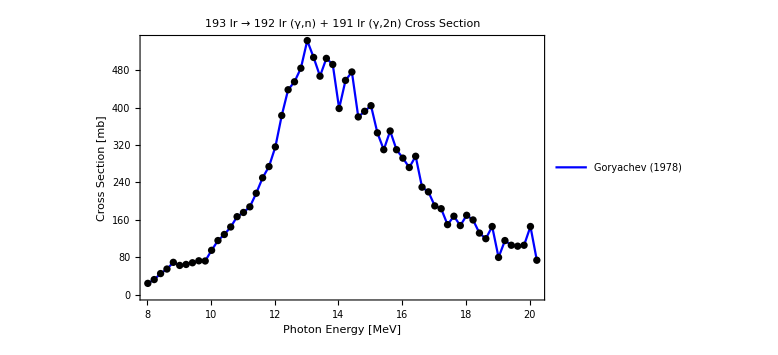

```mathematica
ListPlot[{Partition[Riffle[Goryachev193Ir192Ir191Ir⟦All,1⟧,Goryachev193Ir192Ir191Ir⟦All,2⟧],2],Partition[Riffle[Goryachev193Ir192Ir191Ir⟦All,1⟧,Goryachev193Ir192Ir191Ir⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"193 Ir → 192 Ir (γ,n) + 191 Ir (γ,2n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Goryachev (1978)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.15}],ImageSize->Large]
```

## Ir 193 → Ir 192 (γ,n) + Os 191 (γ,np) + Ir 191 (γ,2n)

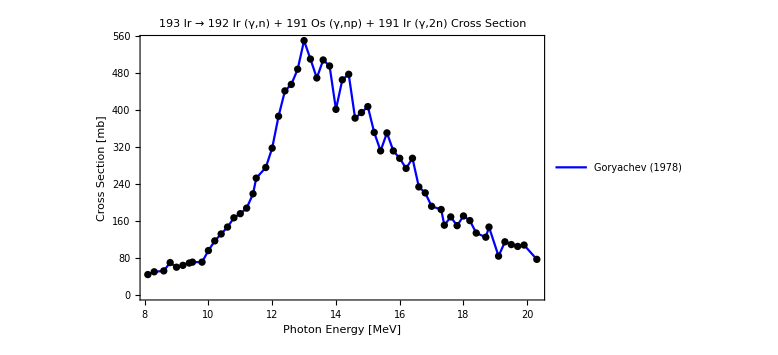

```mathematica
ListPlot[{Partition[Riffle[Goryachev193Ir192Ir191Os191Ir⟦All,1⟧,Goryachev193Ir192Ir191Os191Ir⟦All,2⟧],2],Partition[Riffle[Goryachev193Ir192Ir191Os191Ir⟦All,1⟧,Goryachev193Ir192Ir191Os191Ir⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"193 Ir → 192 Ir (γ,n) + 191 Os (γ,np) + 191 Ir (γ,2n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Goryachev (1978)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.15}],ImageSize->Large]
```

## Ir 191 → Ir 190 (γ,n) + Ir 189 (γ,2n)

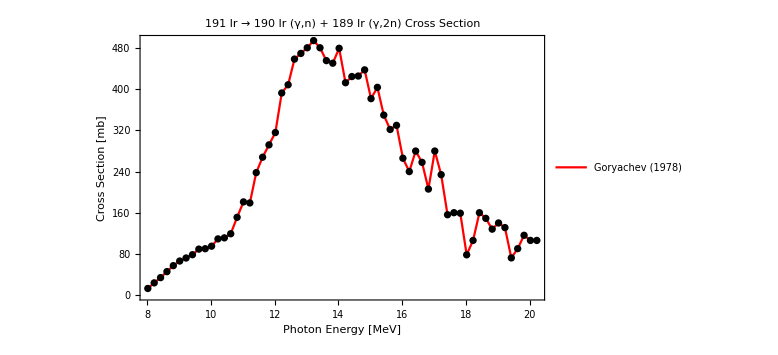

```mathematica
ListPlot[{Partition[Riffle[Goryachev191Ir190Ir189Ir⟦All,1⟧,Goryachev191Ir190Ir189Ir⟦All,2⟧],2],Partition[Riffle[Goryachev191Ir190Ir189Ir⟦All,1⟧,Goryachev191Ir190Ir189Ir⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"191 Ir → 190 Ir (γ,n) + 189 Ir (γ,2n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Goryachev (1978)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.15}],ImageSize->Large]
```

## Ir 191 → Ir 190 (γ,n) + Os 189 (γ,np) + Ir 189 (γ,2n)

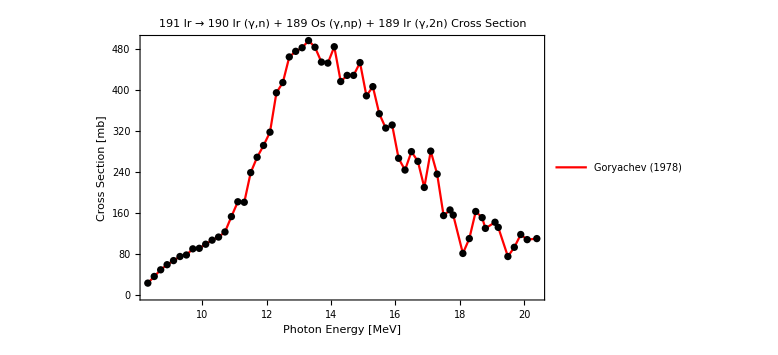

```mathematica
ListPlot[{Partition[Riffle[Goryachev191Ir190Ir189Os189Ir⟦All,1⟧,Goryachev191Ir190Ir189Os189Ir⟦All,2⟧],2],Partition[Riffle[Goryachev191Ir190Ir189Os189Ir⟦All,1⟧,Goryachev191Ir190Ir189Os189Ir⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"191 Ir → 190 Ir (γ,n) + 189 Os (γ,np) + 189 Ir (γ,2n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Goryachev (1978)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.15}],ImageSize->Large]
```

## Iridium Landscape

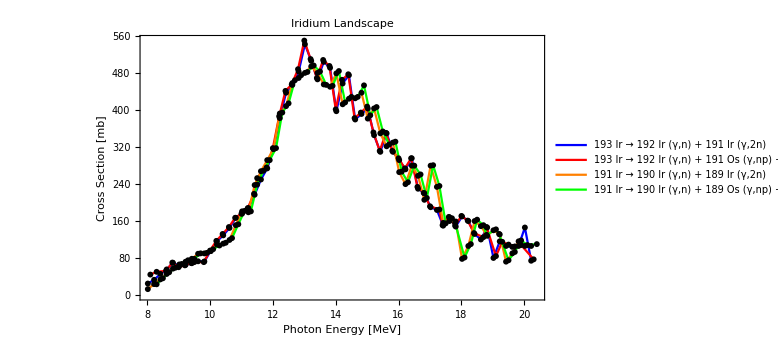

```mathematica
ListPlot[{Partition[Riffle[Goryachev193Ir192Ir191Ir⟦All,1⟧,Goryachev193Ir192Ir191Ir⟦All,2⟧],2],Partition[Riffle[Goryachev193Ir192Ir191Ir⟦All,1⟧,Goryachev193Ir192Ir191Ir⟦All,2⟧],2],Partition[Riffle[Goryachev193Ir192Ir191Os191Ir⟦All,1⟧,Goryachev193Ir192Ir191Os191Ir⟦All,2⟧],2],Partition[Riffle[Goryachev193Ir192Ir191Os191Ir⟦All,1⟧,Goryachev193Ir192Ir191Os191Ir⟦All,2⟧],2],Partition[Riffle[Goryachev191Ir190Ir189Ir⟦All,1⟧,Goryachev191Ir190Ir189Ir⟦All,2⟧],2],Partition[Riffle[Goryachev191Ir190Ir189Ir⟦All,1⟧,Goryachev191Ir190Ir189Ir⟦All,2⟧],2],Partition[Riffle[Goryachev191Ir190Ir189Os189Ir⟦All,1⟧,Goryachev191Ir190Ir189Os189Ir⟦All,2⟧],2],Partition[Riffle[Goryachev191Ir190Ir189Os189Ir⟦All,1⟧,Goryachev191Ir190Ir189Os189Ir⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red,Black,Orange,Black,Green},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Iridium Landscape",PlotLegends->Placed[LineLegend[{None,"193 Ir → 192 Ir (γ,n) + 191 Ir (γ,2n)",None,"193 Ir → 192 Ir (γ,n) + 191 Os (γ,np) + 191 Ir (γ,2n)",None,"191 Ir → 190 Ir (γ,n) + 189 Ir (γ,2n)",None,"191 Ir → 190 Ir (γ,n) + 189 Os (γ,np) + 189 Ir (γ,2n)"},LabelStyle->{10,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.15}],ImageSize->Large]
```

## Samarium 153 Investigation

Notes
• 153 Sm is used as a β^- emitter for palliative treatment of bone metastases. The radiopharmaceutical names for 153 Sm products are Quadramet (made by Lantheus) and Lexidronam (made by Dow Chemical).
• 153 Sm has t_(1/2)=1.93 days, it decays solely by β^-.
• Samarium  has 5 stable isotopes: 144 Sm, 149 Sm, 150 Sm, 152 Sm and 154 Sm. Abundance (3.07%, 13.82%, 7.38%, 26.75%, 22.75%).
• Samarium has 2 quasi-stable isotopes: 147 Sm and 148 Sm. Abundance (14.99%, 11.24%)
• Samarium forms no known hexafluorides, so centrifuge separation seems to be out of question (no vollatile compound). There are chemical separation methods which seem to exist. 
• There seems to be no clear cyclotron production route for 153 Sm. 
• The main research reactor production routes for 153 Sm are:
	• 152 Sm → 153 Sm (n,γ)
	• 154 Sm → 153 Sm (n,2n)
	• There are also Gadolinium target routes to 153 Sm, via an α particle:
		• 155 Gd → 152 Sm (n,α) → 153 Sm (n,γ)
		• 156 Gd → 153 Sm (n,α)
		• 157 Gd → 154 Sm (n,α) → 153 Sm (n,2n)  
	• The main contamination of 153 Sm is with 154 Eu (t_(1/2)=8.59 years), due to the short decay of Sm 153 + it’s reactor production. This results in short shelf life 153 Sm radiopharmaceuticals. The contamination mechanism is:
		• 153 Sm → 153 Eu (β^- decay) → 154 Eu (neutron capture)
	• There are lots of papers on reactor production from Malaysia, India etc. but not western - is this due to commercialisation?
• The photonuclear production mechanisms are:
	• 154 Sm → 153 Sm (γ,n) (Filipescu - NewSUBARU data)
	• 157 Ga → 153 Sm (γ,α) no data	
• The disruptor routes for a 154 Sm target are:
	• 154 Sm → 152 Sm (γ,2n)
	• 154 Sm → Sm (γ,(3+)n) no data
	•154 Sm → Sm (γ,p) no data
	• 154 Sm → 153 Sm (γ,np) with a 16.5 MeV threshold.
	• 154 Sm → 150 Nd (γ,α) no data
• The additional disruptor routes for a bulk Sm target are numerous, but not shown yet for brevity (and my sanity)!

```mathematica
SetDirectory[NotebookDirectory[]];
Filipescu154Sm153Sm=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Samarium153/154Sm (g,n)/Filipescu_154Sm_to_153Sm.txt","Table"],2];
Carlos154Sm153Sm=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Samarium153/154Sm (g,n)/Carlos_154Sm_to_153Sm.txt","Table"],2];

Carlos154Sm152Sm=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Samarium153/154Sm (g,2n)/Carlos_154Sm_to_152Sm.txt","Table"],2];

Carlos154Sm153Sm152Pm=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Samarium153/154Sm (g,np)/Carlos_154Sm_to_153Sm152Pm.txt","Table"],2];
```

## 154 Sm → 153 Sm (γ,n)

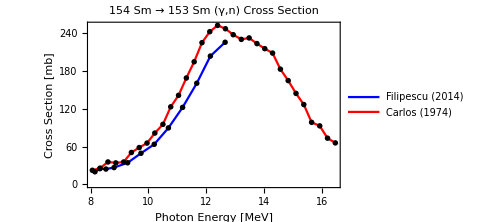

```mathematica
ListPlot[{Partition[Riffle[Filipescu154Sm153Sm⟦All,1⟧,Filipescu154Sm153Sm⟦All,2⟧],2],Partition[Riffle[Filipescu154Sm153Sm⟦All,1⟧,Filipescu154Sm153Sm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm153Sm⟦All,1⟧,Carlos154Sm153Sm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm153Sm⟦All,1⟧,Carlos154Sm153Sm⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"154 Sm → 153 Sm (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Filipescu (2014)",None,"Carlos (1974)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.7,0.15}],ImageSize->Medium]
```

## 154 Sm → 152 Sm (γ,n)

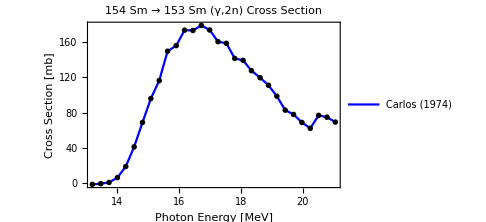

```mathematica
ListPlot[{Partition[Riffle[Carlos154Sm152Sm⟦All,1⟧,Carlos154Sm152Sm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm152Sm⟦All,1⟧,Carlos154Sm152Sm⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"154 Sm → 153 Sm (γ,2n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Carlos (1974)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.2}],ImageSize->Medium]
```

## 154 Sm → 153 Sm (γ,n) + 152 Pm (γ,np)

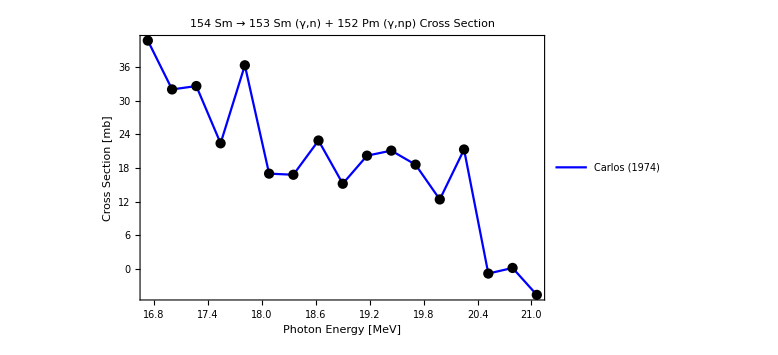

```mathematica
ListPlot[{Partition[Riffle[Carlos154Sm153Sm152Pm⟦All,1⟧,Carlos154Sm153Sm152Pm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm153Sm152Pm⟦All,1⟧,Carlos154Sm153Sm152Pm⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"154 Sm → 153 Sm (γ,n) + 152 Pm (γ,np) Cross Section",PlotLegends->Placed[LineLegend[{None,"Carlos (1974)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.7,0.75}],ImageSize->Large]
```

## 154 Samarium Landscape

• The 154 Samarium landscape for photonuclear production of 153 Sm from a mono-isotopic target.

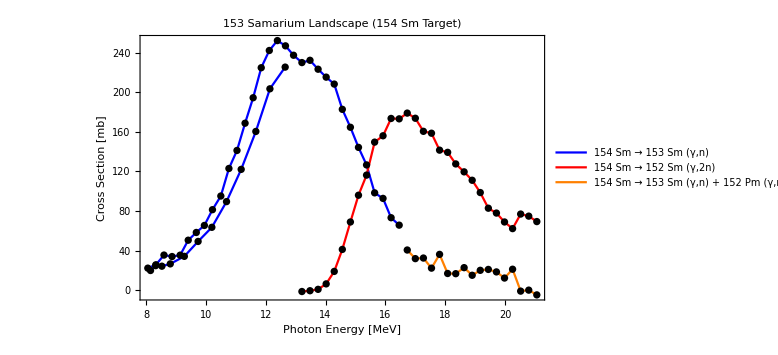

```mathematica
ListPlot[{Partition[Riffle[Filipescu154Sm153Sm⟦All,1⟧,Filipescu154Sm153Sm⟦All,2⟧],2],Partition[Riffle[Filipescu154Sm153Sm⟦All,1⟧,Filipescu154Sm153Sm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm153Sm⟦All,1⟧,Carlos154Sm153Sm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm153Sm⟦All,1⟧,Carlos154Sm153Sm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm152Sm⟦All,1⟧,Carlos154Sm152Sm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm152Sm⟦All,1⟧,Carlos154Sm152Sm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm153Sm152Pm⟦All,1⟧,Carlos154Sm153Sm152Pm⟦All,2⟧],2],Partition[Riffle[Carlos154Sm153Sm152Pm⟦All,1⟧,Carlos154Sm153Sm152Pm⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Blue,Black,Red,Black,Orange},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"153 Samarium Landscape (154 Sm Target)",PlotLegends->Placed[LineLegend[{None,"154 Sm → 153 Sm (γ,n)",None,None,None,"154 Sm → 152 Sm (γ,2n)",None,"154 Sm → 153 Sm (γ,n) + 152 Pm (γ,np)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.85}],ImageSize->Large]
```

## Promethium 149 Investigation

Notes
• 149 Pm is used as a β^- emitter similar to153 Sm and 177 Lu. It appears to have been less tested. There is bombesin data, i.e. labelling for this isotope. It also decays by γ-ray so could be used for in vitro treatment monitoring.
• 153 Sm has t_(1/2)= 2.21 days, it decays by β^- (95.9%) and by producing a γ-ray (3%).
• No stable isotopes of Promethium, so has be be produce via a two stage decay, mostly from Neodymium targets. This does mean that no carrier added 149 Pm can be produced.
• Seemingly all production routes aim to produce 149 Nd, with a half life t_(1/2)= 1.73 hours. 
• Neodymium has 5 stable isotopes: 142 Nd, 143 Nd, 145 Nd, 146 Nd and 148 Nd. Abundance (27.2%, 12.2%, 8.3%, 17.2%, 5.7%)
• Neodymium has 2 quasi-stable isotopes: 144 Nd and 150 Sm. Abundance (23.8%, 5.6%)
• Neodymium forms no known hexafluorides, so centrifuge separation seems to be out of question (no vollatile compound). There are chemical separation methods such as specific extraction chromatography. 
• There seems to be no clear cyclotron production route for 149 Pm. 
• The main research reactor production route for 149 Pm is:
	• 148 Nd → 149 Nd (n,γ) → 149 Pm (β^-, 95.9%)
• The photonuclear production mechanisms are:
	• 150 Nd → 149 Nd (γ,n) → 149 Pm (β^-, 95.9%) 
	• 153 Eu → 148 Pm (γ,α) no data	
• The disruptor routes for a 150 Nd target are:
	• 150 Nd → 148 Nd (γ,2n)
	• 150 Nd → Nd (γ,(3+)n) no data
	• 150 Nd → Nd (γ,(1+)p) no data
	• 150 Nd → Nd (γ,α) no data

```mathematica
SetDirectory[NotebookDirectory[]];
Carlos150Nd149Nd=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Promethium149/150Nd (g,n)/Carlos_150Nd_to_149Nd.txt","Table"],2];

Carlos150Nd148Nd=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Promethium149/150Nd (g,2n)/Carlos_150Nd_to_148Nd.txt","Table"],2];

Carlos150Nd149Nd148Pr=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Promethium149/150Nd (g,np)/Carlos_150Nd_to_149Nd148Pr.txt","Table"],2];
```

## 150 Nd → 149 Nd (γ,n)

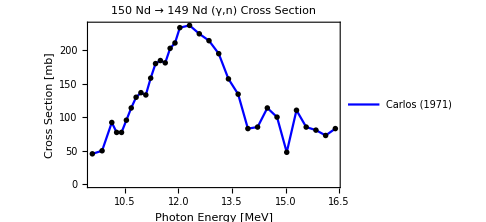

```mathematica
ListPlot[{Partition[Riffle[Carlos150Nd149Nd⟦All,1⟧,Carlos150Nd149Nd⟦All,2⟧],2],Partition[Riffle[Carlos150Nd149Nd⟦All,1⟧,Carlos150Nd149Nd⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"150 Nd → 149 Nd (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Carlos (1971)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.75}],ImageSize->Medium]
```

## 150 Nd → 149 Nd (γ,n) + 148 Pr (γ,np)

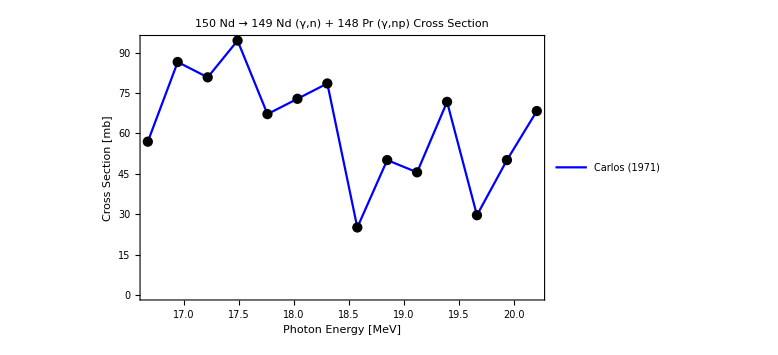

```mathematica
ListPlot[{Partition[Riffle[Carlos150Nd149Nd148Pr⟦All,1⟧,Carlos150Nd149Nd148Pr⟦All,2⟧],2],Partition[Riffle[Carlos150Nd149Nd148Pr⟦All,1⟧,Carlos150Nd149Nd148Pr⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"150 Nd → 149 Nd (γ,n) + 148 Pr (γ,np) Cross Section",PlotLegends->Placed[LineLegend[{None,"Carlos (1971)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.15}],ImageSize->Large]
```

## 150 Nd → 148 Nd (γ,2n)

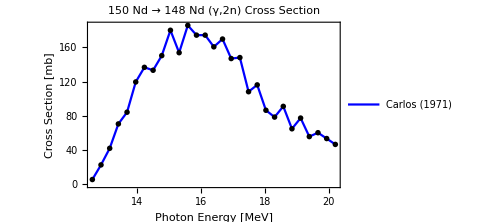

```mathematica
ListPlot[{Partition[Riffle[Carlos150Nd148Nd⟦All,1⟧,Carlos150Nd148Nd⟦All,2⟧],2],Partition[Riffle[Carlos150Nd148Nd⟦All,1⟧,Carlos150Nd148Nd⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"150 Nd → 148 Nd (γ,2n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Carlos (1971)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.2}],ImageSize->Medium]
```

## 150 Neodymium Landscape (Toward 149 Pm)

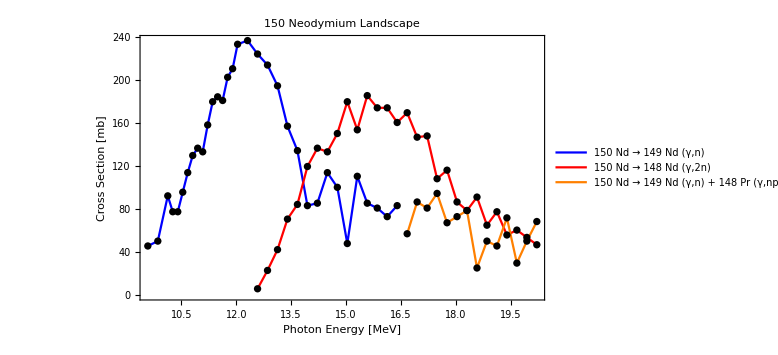

```mathematica
ListPlot[{Partition[Riffle[Carlos150Nd149Nd⟦All,1⟧,Carlos150Nd149Nd⟦All,2⟧],2],Partition[Riffle[Carlos150Nd149Nd⟦All,1⟧,Carlos150Nd149Nd⟦All,2⟧],2],Partition[Riffle[Carlos150Nd148Nd⟦All,1⟧,Carlos150Nd148Nd⟦All,2⟧],2],Partition[Riffle[Carlos150Nd148Nd⟦All,1⟧,Carlos150Nd148Nd⟦All,2⟧],2],Partition[Riffle[Carlos150Nd149Nd148Pr⟦All,1⟧,Carlos150Nd149Nd148Pr⟦All,2⟧],2],Partition[Riffle[Carlos150Nd149Nd148Pr⟦All,1⟧,Carlos150Nd149Nd148Pr⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red,Black,Orange},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"150 Neodymium Landscape",PlotLegends->Placed[LineLegend[{None,"150 Nd → 149 Nd (γ,n)",None,"150 Nd → 148 Nd (γ,2n)",None,"150 Nd → 149 Nd (γ,n) + 148 Pr (γ,np)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.88}],ImageSize->Large]
```

## Rubidium 82

Notes
• 82 Rb is used as a short lived β^+ emitter . This can be used for Myocardial Perfusion scans by PET. Thought to be better than 201 Tl, 99m Tc SPECT. Sequential scans every 10 min since short lived. 
• 82 Rb has t_(1/2)= 75 s, it decays by β^+ (100%). Produced via an 82 Sr generator t_(1/2) = 25.55 days.
• Generator reaction is 82 Sr → 82 Rb (EC, 100%)
• Rubidium has 1 stable isotope + 1 quasi stable: 85 Rb (72.17%), 87 Rb (27.83%) [QS].
• Strontium has 4 stable isotopes: 84 Sr (0.56%), 86 Sr (9.86%), 87 Sr (7%), 88 Sr (82.58%).
• Neither Rubidium or Strontium form a known hexafluoride, so centrifuge separation seems to be out of question (no vollatile compound). I believe there are chemical separation methods. 
• Cyclotron production of 82 Sr generator is produced via:
	•  85 Rb → 82 Sr (p,4n)
	• However this is from bulk Rb and requires 48 MeV protons. Doesn’t seem ideal to me.
• There doesn’t appear to be a reactor production route.
• The photonuclear production mechanisms are:
	• 84 Sr → 82  Sr (γ,2n) with no data. Requires enrichment of 84 Sr.
	• 78 Kr → 82 Sr (γ,α)  with no data. Requres enrichment of 78 Kr, which has a hexafluoride KrF_6. Assume low cross section.
• The disruptor routes for a 84 Sr target aren’t looked at as it seems tenuous.

## Erbium 165

Notes
• 165 Er is used for Targeted Auger Therapy.
• 165 Er has t_(1/2)= 10.36 hours, it decays by electron capture (100%). Produced either directly or via a 165 Tm generator t_(1/2) = 1.25 days.
• Generator reaction is 165 Tm → 165 Er (β^+, 100%)
• Erbium has 5 stable isotopes + 1 quasi stable: 162 Er (0.139%), 164 Er (1.601%), 166 Er (33.503%), 167 Er (22.869%), 168 Er (26.978%), 170 Er (14.91%) [QS].
• Erbium doesn’t form a known hexafluoride, so centrifuge separation seems to be out of question (no vollatile compound). I believe there are chemical separation methods. There is also a laser isotope separation patent from the DoE (1995).
• The cyclotron production routes of 165 Er are:
	•  nat Er → 165 Tm (p,xn) → 165 Er (β^+, 100%). No carrier added for 8 - 15 MeV protons.
	• 166 Er → 165 Tm (p, 2n) → 165 Er (β^+,100%). 166 Tm and 164 Tm impurities? How can this be in the (p,2n) route but not nat Er route?
	• 165 Ho → 165 Er (p,n). Direct route, no generator. Separating Ho and Er is tricky but can be done using LN2 resin separation.
	• 165 Ho → 165 Er (d,2n). Direct route, 8 - 11 MeV is no carrier added.
• The ISOL method appears to use a Tantalum Ion beam on an Aluminium target.	
• Reactor production routes aren’t mentioned in the literature, however this seems possible:
	• 164 Er → 165 Er (n,γ) which is probably not used due to low abundance.
• The photonuclear production mechanisms are:
	• 166 Er → 165  Er (γ,n) with no experimental data
	• 167 Er → 165 Er (γ,2n) no data
	• 168 Er → 165 Er (γ,3n) no data
	• 170 Er → 170 Er (γ,5n) no data
	• Could a multicolour ICS source on bulk Erbium be an option? Would be diffiult to calibrate so we didn’t hit unwanted resonances, maybe possible?
• The disruptor routes for a 166 Er or bulk Er target haven’t been looked at yet. There is a distinct lack of data for this one.

```mathematica
Vagena166Er165ErGLO={{8.5,119},{14,119}};
Vagena166Er165ErSLO={{8.5,135},{14,135}};
```

The Vagena + Stoulos paper for this one provides theoretical predictions of the average cross section within an energy range by the TALYS code. This code uses two particular models: Kopecky-Uhl model (Generalised Lorentzian) or Axel-Brink (Standardized Lorentzian).

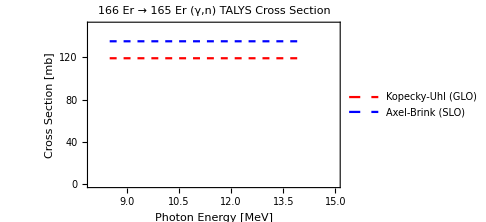

```mathematica
ListPlot[{Vagena166Er165ErGLO,Vagena166Er165ErSLO},Joined->{True,True},PlotStyle->{{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"166 Er → 165 Er (γ,n) TALYS Cross Section",PlotLegends->Placed[LineLegend[{"Kopecky-Uhl (GLO)","Axel-Brink (SLO)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.7,0.45}],PlotRange->{{8,15},{0,150}},ImageSize->Medium]
```

## Indium 111

Notes
• 111 In is used for SPECT imaging. Particularly, it has found use in neuroendocrine tumours + cell labelling. May eventually be replaced by 89 Zr and 68 Ga.
• 111 In Pentetreotide is the imaging form. Trade name is OctreoScan.
• 111 In has t_(1/2)= 2.80 days, it decays by electron capture (100%). 
• Indium has one stable isotope + 1 quasi-stable: 113 In (4.29%), 115 In (95.71%) [QS].
• Indium forms no known volatile compound. It can be separated isotopically by ion exchange chromatography. Possible also by laser isotope separation.
• Tin has 9 stable isotopes and 1 quasi-stable isotope: 112 Sn (0.97%), 114 Sn (0.66%), 115 Sn (0.34%), 116 Sn (14.54%), 117 Sn (7.68%), 118 Sn (24.22%), 119 Sn (8.59%), 120 Sn (32.58%), 122 Sn (4.63%), 124 Sn (5.79%) [QS].
• Tin forms Stannane, otherwise known as Tin Hydride SnH_4. This can be used in centrifuge enrichment. Other methods may be possible.
• The cyclotron production routes of 111 In are:
	•  111 Cd → 111 In (p,n) 
	• 112 Cd → 111 In (p,2n)
• ISOL method has been considered at TRIUMF, however not many details on this.
• Reactor production routes aren’t mentioned in the literature, they don’t seem particularly plausible to me.
• The photonuclear production mechanisms are:
	• 113 In → 111 In (γ,2n) no data just ratios.
	• 112 Sn → 111 Sn (γ,n) → 111 In (β^+, 100%). 111 Sn t_(1/2) = 35.3 min, so a short lived  state.
• The disruptor routes haven’t been looked at yet.

```mathematica
SetDirectory[NotebookDirectory[]];
KuoChiTi112Sn111Sn=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Indium111/112Sn (g,n)/KuoChiTi_112Sn_to_111Sn.txt","Table"],2];
Varlamov112Sn111Sn=Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Medical_Isotopes/Indium111/112Sn (g,n)/Varlamov_112Sn_to_111Sn.txt","Table"],2];
```

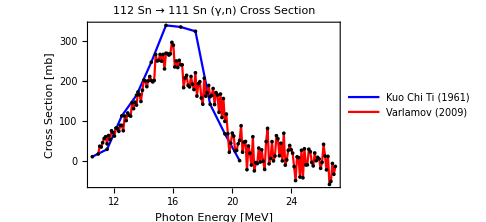

```mathematica
ListPlot[{Partition[Riffle[KuoChiTi112Sn111Sn⟦All,1⟧,KuoChiTi112Sn111Sn⟦All,2⟧],2],Partition[Riffle[KuoChiTi112Sn111Sn⟦All,1⟧,KuoChiTi112Sn111Sn⟦All,2⟧],2],Partition[Riffle[Varlamov112Sn111Sn⟦All,1⟧,Varlamov112Sn111Sn⟦All,2⟧],2],Partition[Riffle[Varlamov112Sn111Sn⟦All,1⟧,Varlamov112Sn111Sn⟦All,2⟧],2]},Joined->{False,True},PlotStyle->{Black,Blue,Black,Red},Frame->True,FrameLabel->{"Photon Energy [MeV]","Cross Section [mb]"},LabelStyle->{16,FontFamily->"Calibri",FontColor->Black},PlotLabel->"112 Sn → 111 Sn (γ,n) Cross Section",PlotLegends->Placed[LineLegend[{None,"Kuo Chi Ti (1961)",None,"Varlamov (2009)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.75}],ImageSize->Medium]
```